```mathematica
Quit[]
```

```mathematica
ClearAll["`*"]
```

# #3: Stochastic Gravitational Wave Background

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
PlotsDir=NotebookDirectory[]<>"results/plots/"
```

/home/buenabad/Documents/codes/git_codes/graphare/results/plots/

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

## Definitions

```mathematica
Clear[GeV,MeV,Mpl,mpl,second,Hz,mHz,h,ρcrit,H0,H0h1,Tγ0,gs0,ge0,gSM,Aρ,ρϕi]
```

### Units

```mathematica
GeV=1;
MeV=10^-3 GeV;
Mpl=1.22091 10^19 GeV;
mpl=Mpl/√(8π);
second=1.519268 10^21/MeV;
Hz=1/second;
mHz=10^-3 Hz;
```

### Constants

```mathematica
h=0.67;
ρcrit=8.0992*10^-47*h^2 GeV^4;
H0=√(ρcrit/(3 mpl^2));
H0h1=H0/h;

Tγ0=(2.4*10^-4)×10^-9 GeV;
gs0=3.94;
ge0=3.38;
gSM=106.75;
```

### Useful

```mathematica
Aρ=gstar π^2/30;
ρϕi=3 Hi^2 mpl^2;
```

## Packages

### InterpolatingFunctionsAnatomy

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

### DSReheating

```mathematica
Needs["DSReheating`"]
```

### PhaseTransition

```mathematica
Needs["PhaseTransition`"]
```

### dePrivFn: De-Privatize Function

Changes context from Package`Private` to Global`:

```mathematica
ContextName["PT"]="PhaseTransition`Private`";
ContextName["RH"]="DSReheating`Private`";

PrivateDict["PT"]={μ,A,λ,Δ,λbar,Mc,M,δ,T,Tc,Ts,T0};
PrivateDict["RH"]={x,rϕ,rr,Hi,gstar,f,γ};
```

```mathematica
Clear[PrivFn,dePrivRule,dePrivFn]

PrivFn[ctxt_,x_]:=ToExpression[ContextName[ctxt]<>ToString[x]]
dePrivRule[ctxt_]:=dePrivRule[ctxt]=PrivFn[ctxt,#]->#&/@PrivateDict[ctxt];
dePrivFn[ctxt_,f_,x___:Null]:=(If[x===Null,If[FailureQ[PrivFn[ctxt,f]],f,PrivFn[ctxt,f]],If[FailureQ[PrivFn[ctxt,f[x]]],f[x],PrivFn[ctxt,f[x]]]])/.dePrivRule[ctxt]
```

Examples:

```mathematica
dePrivFn["PT",Ectwa,λbar]
dePrivFn["PT",EcAn,λbar]
Assuming[9/8>λbar>1,%//Simplify]
dePrivFn["PT",EcAnHot,λbar]
dePrivFn["PT",EcAn,1.1]
```

(2 π (-3+√(9-8 λbar)+4 λbar)^2)/(81 (-1+λbar)^2)

Which[0≤λbar<1,PhaseTransition`Private`EcAnCold[λbar],9/8≥λbar>1,PhaseTransition`Private`EcAnHot[λbar],λbar==1,∞]

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

10.3373

```mathematica
dePrivFn["RH",RHDict["solsAn"]["γ<<1","ϕD"]]
```

{rϕ[x]→4/(9 x^2)-(2 (-2+3 x) (2+3 x) γ)/(81 x^3),rr[x]→1/20 (-(32 (2/3)^(2/3))/(9 x^(8/3))+16/(3 x)) γ}

## Import data

GW experiments

```mathematica
GWLISASensitivity=<<data/GWLISASensitivity.m;
GWETSensitivity=<<data/GWETSensitivity.m;
GWBBOSensitivity=<<data/GWBBOSensitivity.m;
GWDECIGOSensitivity=<<data/GWDECIGOSensitivity.m;
```

## For plots

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}"}]
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2,fticksRNoLabels,fticksR2NoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(* Axis for Epsilon versus mass, but with y-axis labels only every 2 decades *)
fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]),10.^(1+x+Log[10,i-10])]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],2}],1]
(* Axis for Epsilon^2 versus mass *)fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR4[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]

fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
fticksR2NoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,"",{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
Clear[SciStr]
SciStr[x_,decimals_:0,latex_:False]:=Block[{X,pref,dex,scstr,string},

X=Log10[x];
dex=Floor[X];
pref=Round[(10^(X-dex))*10^decimals]*10^-decimals;

scstr=If[latex,StringReplace[ToString[StringForm["`1`\\times 10^(`2`)",pref,dex]],"`"->""],StringReplace[ToString[StringForm["`1`×10^(`2`)",pref,dex]],"\`"->""]];

string=If[MemberQ[{-1,0,1},dex],ToString[(Round[x*10^decimals]/10^decimals)//N],scstr];

Return[string]
]
```

## Phase Transition

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&1>Δ>0&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

Let us look, for example, at the dimensionless bubble energy (Ē)_c(λ̄)

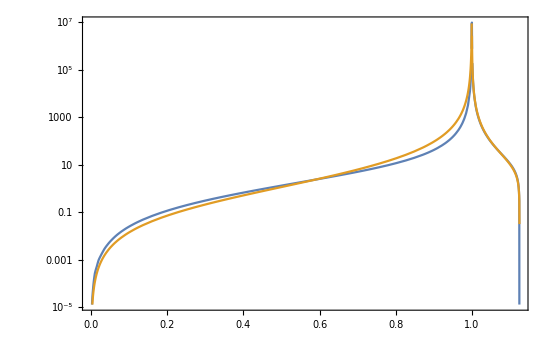

```mathematica
LogPlot[{dePrivFn["PT",EcFn,λbar],dePrivFn["PT",EcAn,λbar]},{λbar,0,9/8},Frame->True]
```

The action is S_E=χ_b^2/(M T)(Ē)_c. For the exact expression for (Ē)_c(λ̄), let’s plot it as a function of θ=T/T_c for varying Δ parameters:

```mathematica
fullSE=(((((dePrivFn["PT",Xb]^2/(dePrivFn["PT",M]*T))*(dePrivFn["PT",EcFn,λbar]/.dePrivFn["PT",McλbarToCoeffs]))/.(dePrivFn["PT",PotToCoeffs]))/.(dePrivFn["PT",ARule]))/.T->Tc*θ)//FullSimplify;
```

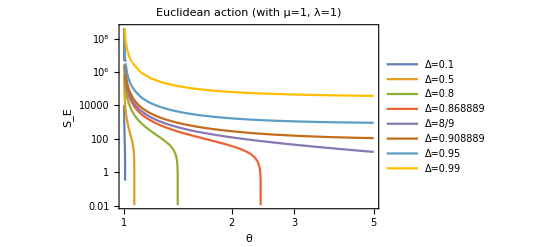

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(fullSE/.{μ->mu,λ->lam,Tc->1})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ","S_E"},PlotLabel->StringForm["Euclidean action (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"full_SE_theta.pdf",%]*)

Clear[ΔTab,mu,lam]
```

In terms of t=T_c/T:

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

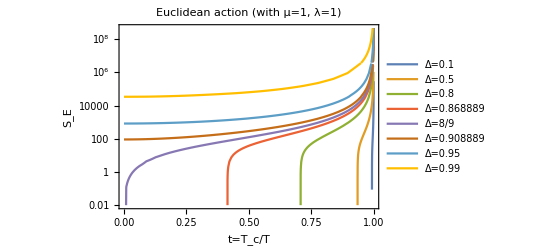

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(fullSE/.{μ->mu,λ->lam,Tc->1,θ->1/t})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogPlot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","S_E"},PlotLabel->StringForm["Euclidean action (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"full_SE_t.pdf",%]*)

Clear[ΔTab,mu,lam]
```

Taking the approximate expression instead:

```mathematica
approxSE=Assuming[ll>0,((((((((dePrivFn["PT",Xb]^2/(dePrivFn["PT",M]*T))*(dePrivFn["PT",EcAnHot,λbar]/.dePrivFn["PT",McλbarToCoeffs]))/.(dePrivFn["PT",PotToCoeffs]))/.(dePrivFn["PT",ARule]))/.{T->Tc*θ,λ->ll^2})//FullSimplify)/.Abs[θ]->θ)//FullSimplify)]/.ll->√λ
```

(2.33313 (9+(-8+8/θ^2)/Δ-8/θ^2)^(3/4) θ^3 (1. Δ^(3/2) θ+0.333333 Δ √(8-8 θ^2+Δ (-8+9 θ^2)))^2 μ)/((-1.+Δ)^2 (-1.+θ^2)^2 √(-1+Δ+θ^2) λ)

We can see that as Δ→8/9 the allowed temperatures become larger and larger (i.e. it takes longer to hit the spinodal temperature, or λ̄=9/8). Eventually, once Δ>8/9, a non-zero minimum action is reached.

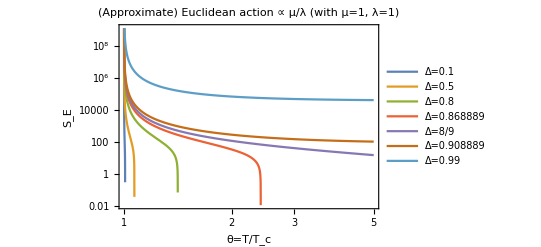

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
(approxSE/.{μ->mu,λ->lam})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ=T/T_c","S_E"},PlotLabel->StringForm["(Approximate) Euclidean action ∝ μ/λ (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"approx_SE_theta.pdf",%]*)

Clear[ΔTab,mu,lam]
```

In terms of t=T_c/T:

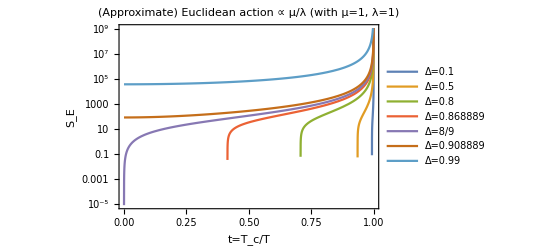

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
Assuming[t>0,(approxSE/.{μ->mu,λ->lam,θ->1/t})//FullSimplify];
(%/.Δ->#&)/@ΔTab;
LogPlot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","S_E"},PlotLabel->StringForm["(Approximate) Euclidean action ∝ μ/λ (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"approx_SE_t.pdf",%]*)

Clear[ΔTab,mu,lam]
```

We can say it differently: λ̄ will reach 9/8 for some temperature θ as long as Δ<8/9, if Δ≥8/9 then λ̄=9/8 is never reached:

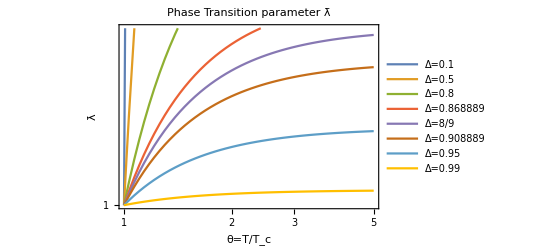

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(((λbar/.dePrivFn["PT",McλbarToCoeffs])/.T->Tc*θ)/.dePrivFn["PT",ARule])//Simplify;
(%/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ=T/T_c","λ̄"},PlotRange->{1,9/8},PlotLabel->"Phase Transition parameter λ̄"]
Clear[ΔTab]
```

In terms of t=T_c/T:

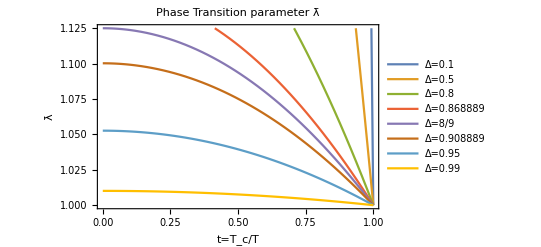

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
Assuming[t>0,(((λbar/.dePrivFn["PT",McλbarToCoeffs])/.T->Tc/t)/.dePrivFn["PT",ARule])//Simplify];
(%/.Δ->#&)/@ΔTab;
Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","λ̄"},PlotRange->{1,9/8},PlotLabel->"Phase Transition parameter λ̄"]

(*Export[PlotsDir<>"lbar_t.pdf",%]*)

Clear[ΔTab]
```

We can then plot Δ(θ) such that λ̄=9/8:

λ̄=(-1+Δ+θ^2)/(Δ θ^2)

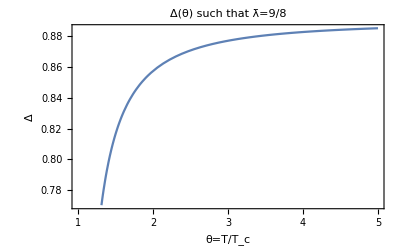

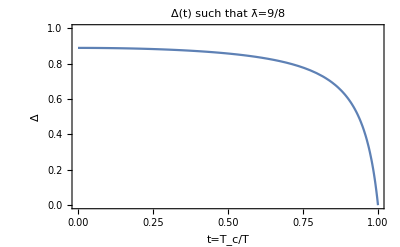

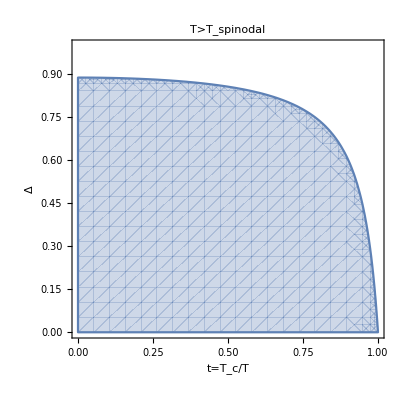

```mathematica
lbar=(((λbar/.dePrivFn["PT",McλbarToCoeffs])/.T->Tc*θ)/.dePrivFn["PT",ARule])//Simplify;

Print["λ̄=",lbar]
Δ/.(Solve[lbar==9/8,Δ]//Flatten);
Plot[%,{θ,1,5},Frame->True,FrameLabel->{"θ=T/T_c","Δ"},PlotLabel->"Δ(θ) such that λ̄=9/8"]
%%/.θ->1/t;
Plot[%,{t,0,1},Frame->True,FrameLabel->{"t=T_c/T","Δ"},PlotLabel->"Δ(t) such that λ̄=9/8",PlotRange->{{0,1},{0,1}}]

RegionPlot[(lbar/.θ->1/t)>9/8,{t,0,1},{Δ,0,1},FrameLabel->{"t=T_c/T","Δ"},PlotLabel->"T>T_spinodal"]
(*Export[PlotsDir<>"spinodal_t-Delta.pdf",%]*)

Clear[lbar]
```

Daisy contributions from a boson scale like ~N g T, where N is some number associated to the degeneracy of the boson in question. The normal contribution to A scales like ~N g⟨χ⟩. We then need to compare T/⟨χ⟩. This factor seems to be irrelevant for most values of Δ, for most temperatures up until the spinodal temperature:

(4 θ^2 λ)/(3 (3 √Δ θ+√(8-8 Δ-8 θ^2+9 Δ θ^2))^2 μ^2)

(9-8 t^2)/(54-54 t^2)

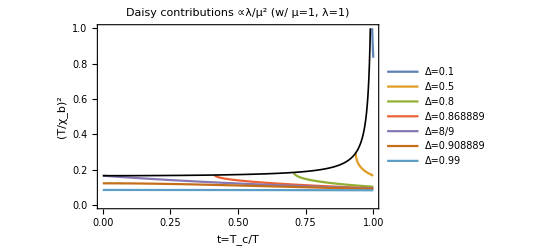

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
daisy=Assuming[ll>0&&Tc>0,((((T/dePrivFn["PT",Xb]/.dePrivFn["PT",PotToCoeffs])/.T->Tc*θ)/.dePrivFn["PT",ARule])/.λ->ll^2)^2//FullSimplify]/.ll->√λ
daisy=(daisy/.{μ->mu,λ->lam,θ->1/t});
Table[daisy,{Δ,ΔTab}];

p1=Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","(T/χ_b)^2"},PlotRange->{0,1},PlotLabel->StringForm["Daisy contributions ∝λ/μ^2 (w/ μ=`1`, λ=`2`)",mu,lam]];

(((λbar/.dePrivFn["PT",McλbarToCoeffs])/.T->Tc*θ)/.dePrivFn["PT",ARule])//Simplify;
(Δ/.(Solve[%==9/8,Δ]//Flatten))/.θ->1/t;
Assuming[t>0,(daisy/.Δ->%)//FullSimplify]
p2=Plot[%,{t,0,1},PlotStyle->{Thickness[0.003],Black},PlotRange->{0,1}];
Show[p1,p2]

(*Export[PlotsDir<>"daisies_t.pdf",%]*)

Clear[ΔTab,daisy,mu,lam,p1,p2]
```

(4 θ^2 λ)/(3 (3 √Δ θ+√(8-8 Δ-8 θ^2+9 Δ θ^2))^2 μ^2)

4/(3 t^2 ((3 √Δ)/t+√(8-8/t^2-8 Δ+(9 Δ)/t^2))^2)

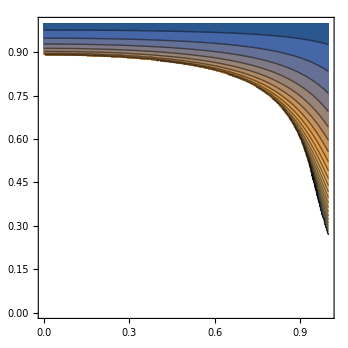

Greater::nord: Invalid comparison with -0.166647-0.00256615 ⅈ attempted.

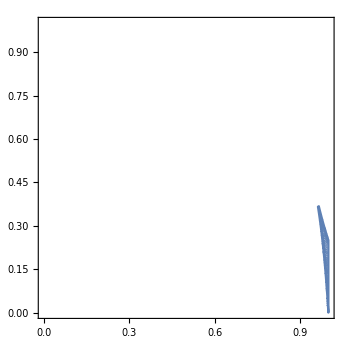

```mathematica
{mu,lam}={1,1};
daisy=Assuming[ll>0&&Tc>0,((((T/dePrivFn["PT",Xb]/.dePrivFn["PT",PotToCoeffs])/.T->Tc*θ)/.dePrivFn["PT",ARule])/.λ->ll^2)^2//FullSimplify]/.ll->√λ
daisy=(daisy/.{μ->mu,λ->lam,θ->1/t})

ContourPlot[Log10[daisy],{t,0,1},{Δ,0,1},Contours->Table[Log10[i],{i,0.01,1,0.01}]]

RegionPlot[daisy>1/3,{t,0,1},{Δ,0,1},MaxRecursion->10]

Clear[mu,lam,daisy]
```

## Reheating

Exact {x_c1,x_max,x_c2}:

{0.74846563997586978968255089523,1.20059126910553545098055292256,4.0495535527402993131195432745}

Approximate {x_c1,x_max,x_c2}:

{0.729167,1.20085,4.26667}

Error [(Approx-Exact)/Exact]:

{-0.0257847,0.000218308,0.0536141}

γ_c^RATE

{0.18670492929890048924294,-0.1910871345582343888577}

-Graphics-

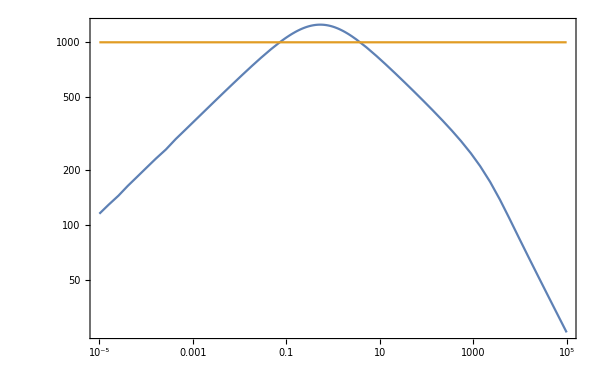

```mathematica
gam=0.001;
regime=If[gam≤1,"γ<<1","γ>>1"];

eff=Max[2/gam^(1/4),2];
rcrit=eff^-4;

res=solEqs[gam];
Print["Exact {x_c1,x_max,x_c2}:"]
xLR=xCross[gam,rcrit]
((dePrivFn["RH",RHDict["xcVals"][regime]])/.{γ->gam,f->eff})//N;
((dePrivFn["RH",RHDict["xMax"][regime]])/.{γ->gam,f->eff})//N;
Print["Approximate {x_c1,x_max,x_c2}:"]
{%%%⟦1⟧,%%,%%%⟦2⟧}
Print["Error [(Approx-Exact)/Exact]:"]
(%%/%%%%%%)-1

domain=InterpolatingFunctionDomain[res⟦2⟧]//Flatten;

Print["γ_c^RATE"]
{gammaRate[gam,xLR⟦1⟧],gammaRate[gam,xLR⟦-1⟧]}

p1=LogLogPlot[{res⟦1⟧[2/3+dx],res⟦2⟧[2/3+dx]},{dx,10^-5,domain⟦2⟧-2/3},PlotRange->{10^-8,100},PlotStyle->{{Blue,Thick},{Red,Thick}},GridLines->{(xLR-2/3)~Join~{1/gam - 2/3},{rcrit}},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\rho/\\rho_{\\phi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_{\\phi}",Magnification->1.7],MaTeX["\\rho_{r}",Magnification->1.7]}],{0.9,0.85}],Epilog->{Inset[Rotate[MaTeX["\\color{black} t=t_\\textrm{max}",Magnification->1.5],90°],Scaled[{.43,.2}]],Inset[Rotate[MaTeX["\\color{black} t=\\Gamma_\\phi^{-1}",Magnification->1.5],90°],Scaled[{.63,.2}]],Inset[Rotate[MaTeX["\\color{black} T=T_c",Magnification->1.5],0°],Scaled[{.08,.55}]],Inset[Rotate[MaTeX[ToString["\\begin{aligned} \\Gamma_\\phi &= "<>ToString[gam]<>"H_i \\end{aligned}"],Magnification->1.3],0°],Scaled[{.13,.9}]]}];

ϕDFns={rϕ[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"ϕD"]]),rr[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"ϕD"]])}/.{γ->gam,f->eff};
RDFns={rϕ[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"RD"]]),rr[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"RD"]])}/.{γ->gam,f->eff};
(ϕDFns~Join~RDFns)/.{x->2/3+dx};

p2=LogLogPlot[%,{dx,10^-5,domain⟦2⟧-2/3},PlotStyle->{{Blue,Dashed,Thickness[0.002]},{Red,Dashed,Thickness[0.002]},{Blue,Dotted,Thickness[0.002]},{Red,Dotted,Thickness[0.002]}},PlotRange->{10^-8,100},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16];

Show[p1,p2]

gSS=10;
TC=1000;
HI=eff^2*(Aρ/.gstar->gSS)*TC^2/(3mpl);
TOfx[gam,gSS,HI];
LogLogPlot[{%[2/3+dx],TC},{dx,10^-5,domain⟦2⟧-2/3},Frame->True,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["T [\\mathrm{GeV}]",Magnification->2]}]

Clear[gam,eff,regime,rcrit,res,xLR,domain,ϕDFns,RDFns,p1,p2,gSS,TC,HI]
```

## Gravitational Wave Spectra

## Stochastic Gravitational Wave Background from First Order Phase Transition (SGWB from 1PT)

## Analytical Approximations

### 1PT: Thin Wall Approximation (TWA)

#### S_E

Computing the action S_E in the TWA:
S_E=E_c/T,   and    E_c=χ_b^2/M(Ē)_c.

```mathematica
EcDim=((dePrivFn[Xb]^2/dePrivFn[M])/.dePrivFn[potCoeffs]);
EcDimless=(dePrivFn[Ectwa,λbar]/.dePrivFn[newdefs]);
SEtwa=(EcDim*EcDimless/T)//Simplify;
```

S_E=Σ/(θ-1)^2

```mathematica
Normal@Series[SEtwa/.T->Tc*θ,{θ,1,-2}]//FullSimplify
Σfac=%*(θ-1)^2;
```

(256 A^5 π)/(27 √3 (-1+θ)^2 λ^(3/2) (4 A^2-3 λ μ^2)^2)

#### |ΔV|

Computing |ΔV|

```mathematica
Assuming[dePrivFn[cond1,μ,A,λ]&&θ>1,((dePrivFn[ΔV]/.dePrivFn[newdefs])/.T->θ*Tc)//Simplify];
Normal@Series[%,{θ,1,1}]
Assuming[dePrivFn[cond1,μ,A,λ]&&0<θ<1,((dePrivFn[ΔV]/.dePrivFn[newdefs])/.T->θ*Tc)//Simplify];
Normal@Series[%,{θ,1,1}]
```

-(16 Tc^4 (-1+θ) (4 A^4-3 A^2 λ μ^2))/(3 λ^3)

(16 Tc^4 (-1+θ) (4 A^4-3 A^2 λ μ^2))/(3 λ^3)

#### χ_b^2

Computing χ_b^2

```mathematica
Assuming[dePrivFn[cond1,μ,A,λ]&&θ>1,((dePrivFn[Xb]/.dePrivFn[potCoeffs])/.T->θ*Tc)//Simplify];
Normal@Series[%^2,{θ,1,1}]
```

(16 A^2 Tc^2)/λ^2-(48 Tc^2 (-1+θ) (-2 A^2+λ μ^2))/λ^2

#### 1PT existence: Δ parameter

First, we start by re-writing the potential coefficient A in terms of the 1PT existence condition:
1-(4 A^2)/(3λ μ^2)>0
⇒ 0<Δ≡(4 A^2)/(3λ μ^2)<1

```mathematica
Assuming[A>0&&λ>0,Solve[Δ==(4 A^2)/(3λ μ^2),A]//FullSimplify]
```

{{A→-1/2 √3 √(Δ λ) μ},{A→1/2 √3 √(Δ λ) μ}}

```mathematica
ARule={A->(√3)/2 √λ μ √Δ};
```

In terms of Δ, the coefficient Σ of the S_E action is:

```mathematica
(Σfac/.ARule)//Simplify
```

(8 π Δ^(5/2) μ)/(27 (-1+Δ)^2 λ)

#### Spinodal temperature T_s

We are interested in the spinodal temperature T_s: when the broken phase minimum disappears:

T_s=T_c/(√(1+A^2/(8 A^2-6λ μ^2))).

Temperatures above the spinodal temperature correspond to those without the broken minimum, and the 1PT cannot take place.

At this temperature, λ̄=(T_c^2+(3/4(λ μ^2)/A^2)(T^2-T_c^2))/T^2 is 9/8:

```mathematica
dePrivFn[Tspinodal](*Subscript[T, s]*)
(((dePrivFn[λbar]/.dePrivFn[newdefs])/.T->Ts)/.%)//Simplify(*λ̄*)
```

{Ts→Tc/(√(1+A^2/(8 A^2-6 λ μ^2)))}

9/8

It is more convenient to write θ_s^2=(T_s/T_c)^2 in terms of Δ:

(8 (-1+Δ))/(-8+9 Δ)

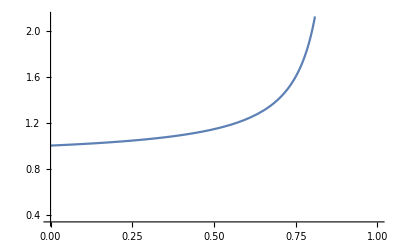

```mathematica
θs2=(((Ts/.dePrivFn[Tspinodal])/Tc)^2/.ARule)//FullSimplify
Plot[θs2,{Δ,0,1}]
```

We find that at Δ_0=8/9 T_s→∞. Therefore, for Δ∈[8/9,1] λ̄ does not reach 9/8 and there is always a spinodal temperature:

(-1+Δ+θ^2)/(Δ θ^2)

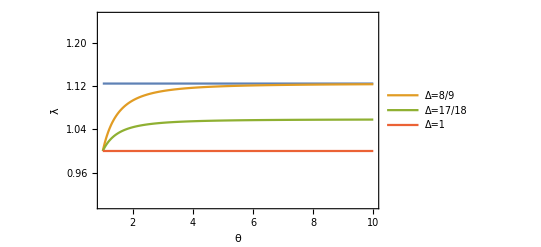

```mathematica
((dePrivFn[λbar]/.dePrivFn[newdefs])/.{T->θ*Tc}~Join~ARule)//Simplify
{9/8}~Join~Table[%,{Δ,{8/9,1-1/18,1}}];
Plot[%,{θ,1,10},PlotRange->{{1,10},{0.9,10/8}},Frame->True,PlotLegends->{None,"Δ=8/9","Δ=17/18","Δ=1"},FrameLabel->{"θ","λ̄"}]
```

So to guarantee that T_s is not reached during the hot 1PT (between x_c1 and x_c2) we need T<T_s for all temperatures probed. This could happen by either taking Δ∈[8/9,1] (thereby bypassing the entire issue of T_s) or by dialing the RH history such that T_max<T_s.

NOTE: If, on the contrary, we have T_s<T_max, this does not necessarily the 1PT will not complete: it may complete at a time x_PT before T reaches T_s at time x_s<x_c2.

#### T_c<T_max<T_s

The simplest way to guarantee as much time for the hot 1PT to complete is to demand T_c<T_max<T_s. The first inequality is a must: otherwise we don’t have a 1PT! On the other hand, the second inequality is not necessary: the 1PT may complete before T reaches T_s. This is simply a convenience.

Recall r_r=(T/(f T_c))^4, so r_(r,s)=f^-4 θ_s^4 and:

r_(r,c)=f^-4<r_(r,max)<r_(r,s)=f^-4 θ_s^4, or

(r_(r,max))^(-1/4)<f<θ_s (r_(r,max))^(-1/4)

```mathematica
fMin["γ<<1"]=rrMax["γ<<1"]^(-1/4)
fMax["γ<<1"]=√θs2 rrMax["γ<<1"]^(-1/4)

fMin["γ>>1"]=rrMax["γ>>1"]^(-1/4)
fMax["γ>>1"]=√θs2 rrMax["γ>>1"]^(-1/4)
```

1/rrMax[γ<<1]^(1/4)

(√θs2)/rrMax[γ<<1]^(1/4)

1/rrMax[γ>>1]^(1/4)

(√θs2)/rrMax[γ>>1]^(1/4)

#### Recap

```mathematica
?Σfac
```

```mathematica
?ARule
```

```mathematica
?θs2
```

```mathematica
?fMin
```

```mathematica
?fMax
```

### ####Thick Wall Approximation

```mathematica
dePrivFn[newdefs]
```

{Mc→(2 A T)/(√3 √λ),λbar→(4 Tc^2+(3 (T-Tc) (T+Tc) λ μ^2)/A^2)/(4 T^2)}

```mathematica
(((dePrivFn[λbar]/.dePrivFn[newdefs])/.{T->Tc*√θ2}~Join~ARule))//Simplify(*λ̄*)
dePrivFn[dimful]
((%/.dePrivFn[newdefs])/.{T->Tc*√θ2}~Join~ARule)//FullSimplify
```

(-1+Δ+θ2)/(Δ θ2)

-(3 Mc^4 λbar (-3 (3+√(9-8 λbar))+4 λbar))/(2 λ)

(3 Tc^4 (-1+Δ+θ2) (4+Δ (-4+9 θ2)+θ2 (-4+3 √((Δ (8-8 Δ-8 θ2+9 Δ θ2))/θ2))) μ^4)/(2 λ)

```mathematica
(dePrivFn[dimful])
```

-(3 Mc^4 λbar (-3 (3+√(9-8 λbar))+4 λbar))/(2 λ)

```mathematica
(dePrivFn[dimlessV,x,λbar])//FullSimplify
%/.{x->1-y}//Expand
(%/.{λbar->9/8-δ});
%/.{y->√ϵ y,δ->ϵ*δ};
Normal@Series[%,{ϵ,0,2}]
```

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

1/4-y^2+y^3-y^4/4-3/(16 λbar)+(9 y^2)/(8 λbar)-(3 y^3)/(2 λbar)+(9 y^4)/(16 λbar)-(√(9-8 λbar))/(16 λbar)+(3 y^2 √(9-8 λbar))/(8 λbar)-(y^3 √(9-8 λbar))/(2 λbar)+(3 y^4 √(9-8 λbar))/(16 λbar)

1/12-1/9 √2 √δ √ϵ-(4 δ ϵ)/27+1/81 (-27 y^3+54 √2 y^2 √δ-8 √2 δ^(3/2)) ϵ^(3/2)+1/972 (243 y^4-864 √2 y^3 √δ+864 y^2 δ-128 δ^2) ϵ^2

```mathematica
(dePrivFn[dimlessV,x,λbar])//FullSimplify
D[%,x]//Simplify;
%/.{x->1-y}//Expand
(%/.{λbar->9/8-δ});
%/.{y->y,δ->ϵ*δ};
Normal@Series[%,{ϵ,0,2}]
```

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

2 y-3 y^2+y^3-(9 y)/(4 λbar)+(9 y^2)/(2 λbar)-(9 y^3)/(4 λbar)-(3 y √(9-8 λbar))/(4 λbar)+(3 y^2 √(9-8 λbar))/(2 λbar)-(3 y^3 √(9-8 λbar))/(4 λbar)

y^2-y^3-4/3 (√2 y √δ-2 √2 y^2 √δ+√2 y^3 √δ) √ϵ-16/9 (y δ-2 y^2 δ+y^3 δ) ϵ-32/27 (√2 y δ^(3/2)-2 √2 y^2 δ^(3/2)+√2 y^3 δ^(3/2)) ϵ^(3/2)-128/81 (y δ^2-2 y^2 δ^2+y^3 δ^2) ϵ^2

```mathematica
6.13 √δ/.δ->0.01
```

0.613

```mathematica
(fy''[r]+2/r fy'[r])/.r->0
%==(-(y[r]^2-y[r]^3-4/3 (√2 y[r] √δ-2 √2 y[r]^2 √δ+√2 y[r]^3 √δ))/.y[r]->fy[r])/.r->0
Solve[%,σ]
```

-(6 y0)/σ^2

-(6 y0)/σ^2==-y0^2+y0^3+4/3 (√2 y0 √δ-2 √2 y0^2 √δ+√2 y0^3 √δ)

{{σ→-(3 √2)/(√(3 y0-3 y0^2-4 √2 √δ+8 √2 y0 √δ-4 √2 y0^2 √δ))},{σ→(3 √2)/(√(3 y0-3 y0^2-4 √2 √δ+8 √2 y0 √δ-4 √2 y0^2 √δ))}}

```mathematica
Normal@Series[(3 √2)/(√(3 y0-3 y0^2-4 √2 √δ+8 √2 y0 √δ-4 √2 y0^2 √δ)),{δ,0,1}]
```

(√6)/(√(-(-1+y0) y0))-(4 (-1+y0) √δ)/(√3 y0 √(-(-1+y0) y0))+(4 √(2/3) (-1+y0)^2 δ)/(y0^2 √(-(-1+y0) y0))

```mathematica
fy[r]/.σ->(√6)/(√(y0-y0^2))
D[%,{r,2}]//Simplify
%/.r->0

(2/r D[%%%,r])/.r->0
(%%+%)//Simplify

((-(y[r]^2-y[r]^3-4/3 (√2 y[r] √δ-2 √2 y[r]^2 √δ+√2 y[r]^3 √δ)))/.{y[r]->fy[r]/.σ->(√6)/(√(y0-y0^2))});
%/.r->0
Solve[%%%==%,y0]
```

ⅇ^(-1/6 r^2 (y0-y0^2)) y0

1/9 ⅇ^(1/6 r^2 (-1+y0) y0) (-1+y0) y0^2 (3+r^2 (-1+y0) y0)

1/3 (-1+y0) y0^2

-2/3 y0 (y0-y0^2)

(-1+y0) y0^2

-y0^2+y0^3+4/3 (√2 y0 √δ-2 √2 y0^2 √δ+√2 y0^3 √δ)

{{y0→0},{y0→1},{y0→1}}

1.115

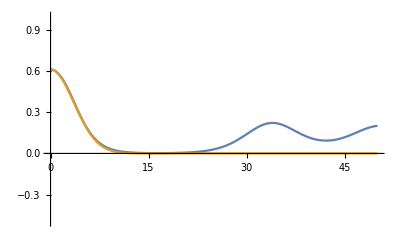

```mathematica
δ=0.01;
9/8 - δ
NDSolve[{y''[r]+2/r y'[r]==-(y[r]^2-y[r]^3-4/3 (√2 y[r] √δ-2 √2 y[r]^2 √δ+√2 y[r]^3 √δ)),y[0.01]==6.13 √δ,y'[0.01]==0},{y[r]},{r,0.01,50}]//Flatten;

Plot[{y[r]/.%,0.613Exp[-r^2/(5.0291)^2]},{r,0.01,50},PlotRange->{-0.5,1}]

Clear[δ]
```

```mathematica
{σ->(√6)/(√(y-y^2))}/.y->(6.13 √δ/.δ->0.01)
```

{σ→5.0291}

```mathematica
Solve[((2 (-9+2 √2 √δ σ^2))/(3 σ^2)/.{δ->0.01})==(6.13 √δ/.δ->0.01),σ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{σ→0.-3.75983 ⅈ},{σ→0.+3.75983 ⅈ}}

```mathematica
ARule
```

{A→1/2 √3 √Δ √λ μ}

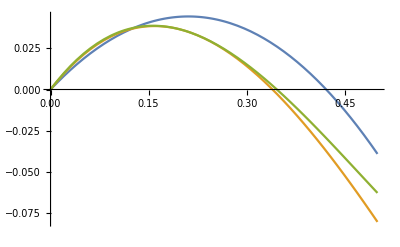

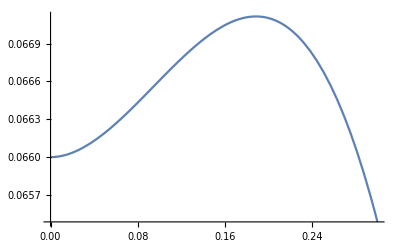

```mathematica
Plot[{-(y^2-4/3 √2 y √δ)/.δ->0.05,-(y^2-4/3 √2 y √δ-y^3+8/3 √2 y^2 √δ-(16 y δ)/9)/.δ->0.05,-((y^2-4/3 √2 y √δ)+(-y^3+8/3 √2 y^2 √δ-(16 y δ)/9)-4/27 (9 √2 y^3 √δ-24 y^2 δ+8 √2 y δ^(3/2)))/.δ->0.05},{y,0,0.5}]
Plot[(1/12-1/9 √2 √δ √ϵ-(4 δ ϵ)/27+1/81 (-27 y^3+54 √2 y^2 √δ-8 √2 δ^(3/2)) ϵ^(3/2))/.{δ->0.01,ϵ->1},{y,0,0.3}]
```

```mathematica
1.125-0.01
```

1.115

```mathematica
DSolve[2/r y'[r]==-(y[r]^2-4/3 √2 y[r] √δ),y[r],r]
```

{{y[r]→(4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1])))}}

```mathematica
Limit[(4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))),r->Infinity]//N
%/.δ->0.05
```

1.88562 √δ

0.421637

```mathematica
((4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1])))/.r->0)/.δ->0.05
```

0.421637/(1-ⅇ^(1.26491 C[1]))

```mathematica
((D[(4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))),{r,1}])/.r->0)//Simplify
```

0

```mathematica
Assuming[δ>0,((D[(4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))),{r,2}]))//Expand]
Limit[%,r->∞]
```

-(16 ⅇ^(2/3 √2 r^2 √δ) δ)/(9 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))^2)+(16 ⅇ^(1/3 √2 r^2 √δ) δ)/(9 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1])))+(64 √2 ⅇ^(√2 r^2 √δ) r^2 δ^(3/2))/(27 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))^3)-(32 √2 ⅇ^(2/3 √2 r^2 √δ) r^2 δ^(3/2))/(9 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))^2)+(32 √2 ⅇ^(1/3 √2 r^2 √δ) r^2 δ^(3/2))/(27 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1])))

0

```mathematica
Assuming[δ>0,((D[(4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))),{r,2}])/.r->∞)]
```

(4 √2 √δ (2/3 √2 ⅇ^(∞ √Sign[δ]) √δ+ⅇ^(∞ √Sign[δ]) δ ∞))/(3 (-ⅇ^(4 √2 √δ C[1])+ⅇ^(∞ √Sign[δ])))+4/3 √2 ⅇ^(∞ √Sign[δ]) √δ (-(2 √2 ⅇ^(∞ √Sign[δ]) √δ)/(3 (-ⅇ^(4 √2 √δ C[1])+ⅇ^(∞ √Sign[δ]))^2)+(ⅇ^(∞ √Sign[δ]) δ (-∞))/((-ⅇ^(4 √2 √δ C[1])+ⅇ^(∞ √Sign[δ]))^2)+(ⅇ^(∞ √Sign[δ]) δ ∞)/((-ⅇ^(4 √2 √δ C[1])+ⅇ^(∞ √Sign[δ]))^3))+(ⅇ^(∞ √Sign[δ]) (-∞) Sign[δ]^(3/2))/((-ⅇ^(4 √2 √δ C[1])+ⅇ^(∞ √Sign[δ]))^2)

```mathematica
((4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))))/.r->0
```

(4 √2 √δ)/(3 (1-ⅇ^(4 √2 √δ C[1])))

```mathematica
D[(4 √2 ⅇ^(1/3 √2 r^2 √δ) √δ)/(3 (ⅇ^(1/3 √2 r^2 √δ)-ⅇ^(4 √2 √δ C[1]))),r]/.r->0
```

0

```mathematica
Limit[(4 √2 ⅇ^(2/3 √2 √δ (r^2-6 C[1])) √δ)/(3 (-1+ⅇ^(2/3 √2 √δ (r^2-6 C[1])))),r->∞]
```

(4 √2 √δ)/3

```mathematica
(2 y-3 y^2+y^3-(9 y)/(4 λbar)+(9 y^2)/(2 λbar)-(9 y^3)/(4 λbar)-(3 y √(9-8 λbar))/(4 λbar)+(3 y^2 √(9-8 λbar))/(2 λbar)-(3 y^3 √(9-8 λbar))/(4 λbar))/.λbar->9/8
```

y^2-y^3

```mathematica
((y^2-4/3 √2 y √δ)/.y->y0*Exp[-r^2/σ^2])
%/.r->0
```

ⅇ^(-(2 r^2)/σ^2) y0^2-4/3 √2 ⅇ^(-r^2/σ^2) y0 √δ

y0^2-4/3 √2 y0 √δ

```mathematica
√(.6)
```

0.774597

NDSolve::ndsz: At r == 4.82357, step size is effectively zero; singularity or stiff system suspected.

{y[r]→InterpolatingFunction[…][r]}

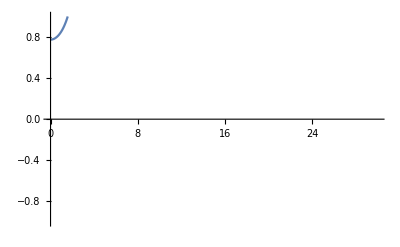

```mathematica
NDSolve[{y''[r]+2/r y'[r]==(y[r]^2-4/3 √2 y[r] √0.01) ,y[0.001]==√(.6),y'[0.001]==0},y[r],{r,0.001,30}]//Flatten
Plot[y[r]/.%,{r,0.001,30},PlotRange->{-1,1}]
```

```mathematica
((y^2-4/3 √2 y √δ)/.y->y0*Exp[-r^2/σ^2])/.r->0

fy[r_]:=y0*Exp[-r^2/σ^2]
2 fy'[r]/r;
fy''[r]//Simplify;
(%%+%)/.r->0
Solve[%==%%%%%,y0]
%/.{σ->10.,δ->0.01}
```

y0^2-4/3 √2 y0 √δ

-(6 y0)/σ^2

{{y0→0},{y0→(2 (-9+2 √2 √δ σ^2))/(3 σ^2)}}

{{y0→0},{y0→0.128562}}

(2 ⅇ^(-r^2/σ^2) y (-2 r^2+3 σ^2))/σ^4

ⅇ^(-(2 r^2)/σ^2) y^2-ⅇ^(-(3 r^2)/σ^2) y^3

{σ→(√6)/(√(y-y^2))}

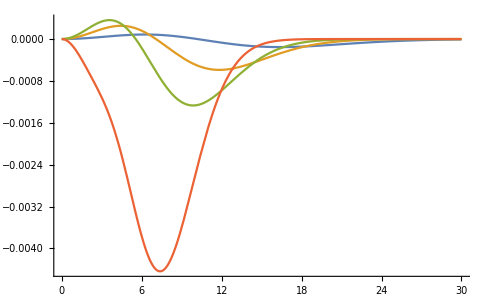

ⅇ^(-(2 r^2)/σ^2) y^2-ⅇ^(-(3 r^2)/σ^2) y^3+(-4/3 √2 ⅇ^(-r^2/σ^2) y+8/3 √2 ⅇ^(-(2 r^2)/σ^2) y^2-4/3 √2 ⅇ^(-(3 r^2)/σ^2) y^3) √ϵ+(-16/9 ⅇ^(-r^2/σ^2) y+32/9 ⅇ^(-(2 r^2)/σ^2) y^2-16/9 ⅇ^(-(3 r^2)/σ^2) y^3) ϵ

-ⅇ^(-(2 r^2)/σ^2) y^2+ⅇ^(-(3 r^2)/σ^2) y^3-(-4/3 √2 ⅇ^(-r^2/σ^2) y+8/3 √2 ⅇ^(-(2 r^2)/σ^2) y^2-4/3 √2 ⅇ^(-(3 r^2)/σ^2) y^3) √ϵ-(-16/9 ⅇ^(-r^2/σ^2) y+32/9 ⅇ^(-(2 r^2)/σ^2) y^2-16/9 ⅇ^(-(3 r^2)/σ^2) y^3) ϵ-(4 ⅇ^(-r^2/σ^2) r^2 y)/σ^4+(6 ⅇ^(-r^2/σ^2) y)/σ^2

ConditionalExpression[1/108 √π y √(1/σ^2) (216+(9 y (-3 √2+2 √3 y)+24 (3 √2+y (-6+√6 y)) √ϵ+32 (3-3 √2 y+√3 y^2) ϵ) σ^2),Re[σ^2]>0]

```mathematica
fx[r_]:=1-y*Exp[-r^2/σ^2]
2 fx'[r]/r;
fx''[r]//Simplify;
(%+%%)//FullSimplify

(dePrivFn[dimlessV,x,λbar])//FullSimplify;
(D[%,x]/.{x->fx[r],λbar->9/8})//Expand
Solve[(%%%/.r->0)==(%/.r->0),σ]⟦2⟧

(fx''[r]+2/r fx'[r]-%%)/.%;
Table[%,{y,{0.05,0.1,0.15,0.3}}];
Plot[%,{r,0,30},PlotRange->All]

(dePrivFn[dimlessV,x,λbar])//FullSimplify;
(D[%,x]/.{x->fx[r],λbar->(9/8)-ϵ});
Collect[Assuming[ϵ>0,Normal@Series[%,{ϵ,0,1}]]//Expand,{ϵ,y}]
(fx''[r]+2/r fx'[r]-%)
Integrate[%,{r,0,∞}]

Clear[fx]
```

```mathematica
Assuming[0<y<1,(1/108 √π y √(1/σ^2) (216+(9 y (-3 √2+2 √3 y)+24 (3 √2+y (-6+√6 y)) √ϵ+32 (3-3 √2 y+√3 y^2) ϵ) σ^2)/.{σ->(√6)/(√(y-y^2))})//FullSimplify]
```

(√π (9 y (4-3 √2+2 (-2+√3) y)+24 (3 √2+y (-6+√6 y)) √ϵ+32 (3-3 √2 y+√3 y^2) ϵ))/(18 √(-6+6/y))

```mathematica
Solve[9 y (4-3 √2+2 (-2+√3) y)+24 (3 √2+y (-6+√6 y)) √ϵ+32 (3-3 √2 y+√3 y^2) ϵ==0,y]
%/.ϵ->0.0000000005
```

{{y→(-36+27 √2+144 √ϵ+96 √2 ϵ-√((36-27 √2-144 √ϵ-96 √2 ϵ)^2-4 (72 √2 √ϵ+96 ϵ) (-36+18 √3+24 √6 √ϵ+32 √3 ϵ)))/(2 (-36+18 √3+24 √6 √ϵ+32 √3 ϵ))},{y→(-36+27 √2+144 √ϵ+96 √2 ϵ+√((36-27 √2-144 √ϵ-96 √2 ϵ)^2-4 (72 √2 √ϵ+96 ϵ) (-36+18 √3+24 √6 √ϵ+32 √3 ϵ)))/(2 (-36+18 √3+24 √6 √ϵ+32 √3 ϵ))}}

{{y→0.00103873},{y→-0.454604}}

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

(27 Mc^4 x^2 (-24 x+18 x^2))/(16 λ)

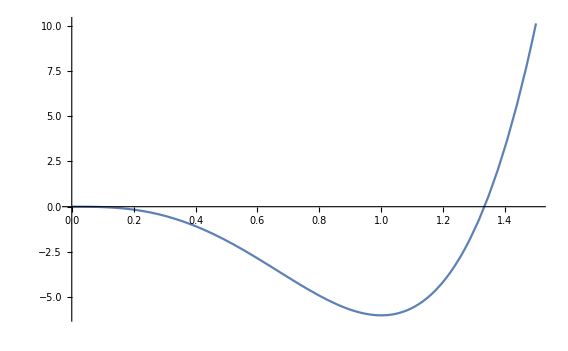

```mathematica
(dePrivFn[dimlessV,x,λbar])
(%*(dePrivFn[dimful]))/.λbar->0
Plot[x^2 (-24 x+18 x^2),{x,0,1.5}]
```

{0.5,1-0.5 ⅇ^(-r^2),1-0.5 ⅇ^(-2 r^2),1-0.5 ⅇ^(-3 r^2)}

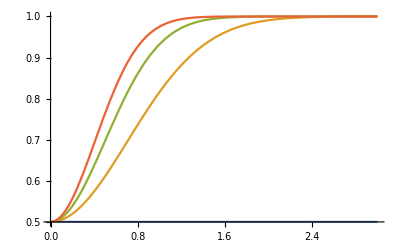

```mathematica
Table[1-0.5Exp[-σ*r^2],{σ,0,3}]
Plot[%,{r,0,3}]
```

```mathematica
(dePrivFn[dimlessV,x,1])//Simplify
```

1/2 (-1+x)^2 x^2

```mathematica
(dePrivFn[dimlessV,x,λbar])
Collect[(D[%,x]//Simplify)/.x->1-y,y]
Collect[Normal@Series[%/.λbar->9/8-ϵ,{ϵ,0,1}],{y,ϵ}]
Collect[Normal@Series[%%/.λbar->ϵ,{ϵ,0,1}],{y,ϵ}]
```

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

-(y (9+3 √(9-8 λbar)-8 λbar))/(4 λbar)-(y^3 (9+3 √(9-8 λbar)-4 λbar))/(4 λbar)-(y^2 (-18-6 √(9-8 λbar)+12 λbar))/(4 λbar)

y^3 (-1-(4 √2 √ϵ)/3-(16 ϵ)/9)+y (-4/3 √2 √ϵ-(16 ϵ)/9)+y^2 (1+(8 √2 √ϵ)/3+(32 ϵ)/9)

y^2 (-5+9/ϵ-(4 ϵ)/9)+y^3 (2-9/(2 ϵ)+(2 ϵ)/9)+y (3-9/(2 ϵ)+(2 ϵ)/9)

```mathematica
DSolve[{2/r y'[r]==-(y[r]^2 -y[r]^3),y[0]==y0},y[r],r]
```

{{y[r]→InverseFunction[Log[1-#1]-Log[#1]+1/#1&][r^2/4+(1+y0 Log[1-y0]-y0 Log[y0])/y0]}}

```mathematica
D[InverseFunction[Log[1-#1]-Log[#1]+1/#1&][r^2/4+(1+y0 Log[1-y0]-y0 Log[y0])/y0],{r,2}];
%/.r->0
%/.y0->0.01
```

1/(2 (-1/(1-InverseFunction[Log[1-#1]-Log[#1]+1/#1&][(1+y0 Log[1-y0]-y0 Log[y0])/y0])-1/(InverseFunction[Log[1-#1]-Log[#1]+1/#1&][(1+y0 Log[1-y0]-y0 Log[y0])/y0])^2-1/(InverseFunction[Log[1-#1]-Log[#1]+1/#1&][(1+y0 Log[1-y0]-y0 Log[y0])/y0])))

-0.0000495

```mathematica
InverseFunction[Log[1-#1]-Log[#1]+1/#1&][r^2/4+(1+y0 Log[1-y0]-y0 Log[y0])/y0]/.y0->0.2
%/.r->1000
```

InverseFunction[Log[1-#1]-Log[#1]+1/#1&][6.38629+r^2/4]

4.0001×10^-6

InverseFunction[Log[1-#1]-Log[#1]+1/#1&][6.38629+r^2/4]

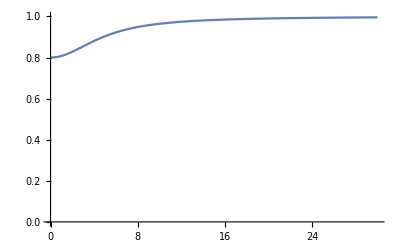

```mathematica
InverseFunction[Log[1-#1]-Log[#1]+1/#1&][r^2/4+(1+y0 Log[1-y0]-y0 Log[y0])/y0]/.y0->0.2
Plot[1-%,{r,0,30},PlotRange->{0,1}]
```

```mathematica
DSolve[{2/r y'[r]==-(y[r] (-4/3 √2 √ϵ-(16 ϵ)/9)+y[r]^2 (1+(8 √2 √ϵ)/3+(32 ϵ)/9)),y[0]==y0},y[r],r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[r]→(4 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0 (3 √2+4 √ϵ) √ϵ)/(-9 y0+9 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0+12 √2 √ϵ-24 √2 y0 √ϵ+24 √2 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0 √ϵ+16 ϵ-32 y0 ϵ+32 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0 ϵ)}}

```mathematica
Limit[(4 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0 (3 √2+4 √ϵ) √ϵ)/(-9 y0+9 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0+12 √2 √ϵ-24 √2 y0 √ϵ+24 √2 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0 √ϵ+16 ϵ-32 y0 ϵ+32 ⅇ^(1/3 √2 r^2 √ϵ+(4 r^2 ϵ)/9) y0 ϵ),r->∞]
```

ConditionalExpression[(4 (3 √2 √ϵ+4 ϵ))/(9+24 √2 √ϵ+32 ϵ),y0∈ℝ&&3 √2 √ϵ+4 ϵ>0]

```mathematica
(4 (3 √2 √ϵ))/(9+24 √2 √ϵ)/.ϵ->0.05
```

0.228744

```mathematica
(4 (3 √2 √ϵ+4 ϵ))/(9+24 √2 √ϵ+32 ϵ)/.ϵ->0.05
```

0.252604

```mathematica
(4 √2 ⅇ^(1/3 √2 r^2 √ϵ) y0 √ϵ)/(-3 y0+3 ⅇ^(1/3 √2 r^2 √ϵ) y0+4 √2 √ϵ-8 √2 y0 √ϵ+8 √2 ⅇ^(1/3 √2 r^2 √ϵ) y0 √ϵ)/.{ϵ->0.01,y0->0.8}
```

(0.452548 ⅇ^(0.0471405 r^2))/(-2.73941+3.3051 ⅇ^(0.0471405 r^2))

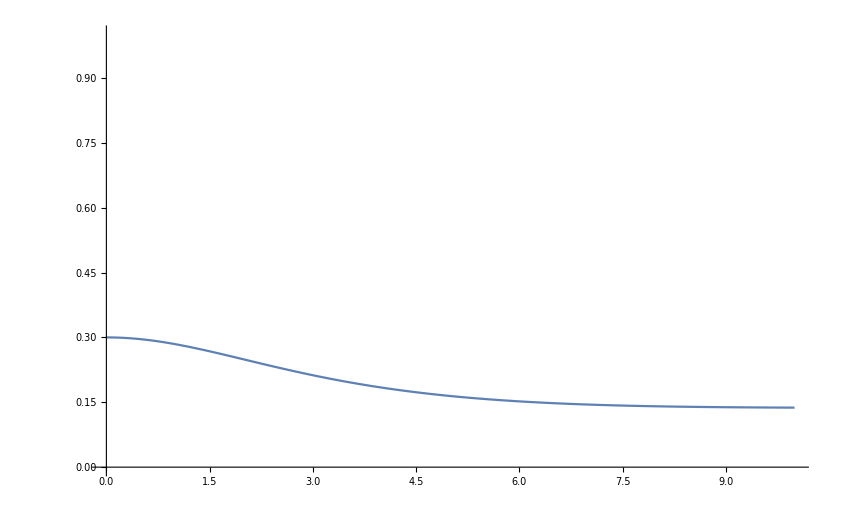

```mathematica
Plot[(4 √2 ⅇ^(1/3 √2 r^2 √ϵ) y0 √ϵ)/(-3 y0+3 ⅇ^(1/3 √2 r^2 √ϵ) y0+4 √2 √ϵ-8 √2 y0 √ϵ+8 √2 ⅇ^(1/3 √2 r^2 √ϵ) y0 √ϵ)/.{ϵ->0.01,y0->0.3},{r,0,10},PlotRange->{0,1}]
```

```mathematica
dePrivFn[dimlessV,x,λbar]
%/.λbar->9/8-ϵ
Collect[Assuming[ϵ>0,Normal@Series[%,{ϵ,0,1}]//Simplify],ϵ]
%/.x->1-y
Normal@Series[%,{y,0,3}]
Collect[%,{ϵ,y}]
```

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

(x^2 (-4 x (3+√(9-8 (9/8-ϵ)))+x^2 (9+3 √(9-8 (9/8-ϵ))-4 (9/8-ϵ))+8 (9/8-ϵ)))/(16 (9/8-ϵ))

1/108 x^2 (54-72 x+27 x^2)+1/108 x^2 (-48 √2 x+36 √2 x^2) √ϵ+1/108 x^2 (-64 x+48 x^2) ϵ

1/108 (54-72 (1-y)+27 (1-y)^2) (1-y)^2+1/108 (-48 √2 (1-y)+36 √2 (1-y)^2) (1-y)^2 √ϵ+1/108 (-64 (1-y)+48 (1-y)^2) (1-y)^2 ϵ

1/27 y^3 (-9-24 √2 √ϵ-32 ϵ)+1/108 (9-12 √2 √ϵ-16 ϵ)+y^2 ((2 √2 √ϵ)/3+(8 ϵ)/9)

```mathematica
((1/12-y^3/3+(-(√2)/9+(2 √2 y^2)/3-(8 √2 y^3)/9) √ϵ)/.ϵ->0.03)//Expand
D[%,y]
```

0.0561168+0.163299 y^2-0.551066 y^3

0.326599 y-1.6532 y^2

```mathematica
-0.5510657549140603 y^3/.y->0.2
```

-0.00440853

```mathematica
0.16329931618554522 y^2/.y->0.2
```

0.00653197

```mathematica
1/12-y^3/3+(-(√2)/9+(2 √2 y^2)/3-(8 √2 y^3)/9) √ϵ+(-4/27+(8 y^2)/9-(32 y^3)/27) ϵ
```

```mathematica
(((-(√2)/9+(2 √2 y^2)/3-(8 √2 y^3)/9) √ϵ)/.ϵ->0.03)//Expand
(((-4/27+(8 y^2)/9-(32 y^3)/27) ϵ)/.ϵ->0.03)//Expand
```

-0.0272166+0.163299 y^2-0.217732 y^3

-0.00444444+0.0266667 y^2-0.0355556 y^3

```mathematica
D[1-α*Exp[-σ*r^2],r]
```

2 ⅇ^(-r^2 σ) r α σ

```mathematica
DSolve[{2/r fx'[r]==fx[r]*(1-fx[r]),fx[0]==1/2},fx[r],r]//Expand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{fx[r]→(ⅇ^(r^2/4))/(1+ⅇ^(r^2/4))}}

1-1/2 ⅇ^(-r^2/4)

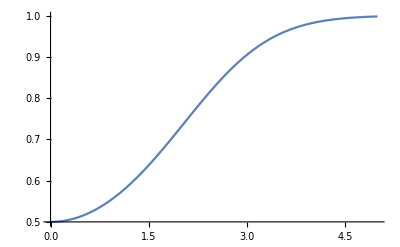

```mathematica
1/2 ⅇ^(-r^2/4) (-1+2 ⅇ^(r^2/4))//Expand
Plot[(ⅇ^(r^2/4))/(1+ⅇ^(r^2/4)),{r,0,5}]
```

```mathematica
WeierstrassP[(-1/6)^(1/3) (r),{0,0}]
```

-((-1)^(1/3) 6^(2/3))/r^2

```mathematica
fx[r_]:=1-α*Exp[-σ*r^2]
((x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)/.{x->fx[r]})//Simplify
fx''[r]+2/r fx'[r]
((%%/.r->0)//Simplify)
(%%/.r->0)//Simplify

Normal@Series[%%/.{λbar->9/8-ϵ},{ϵ,0,1}]
Clear[fx]
```

((-1+ⅇ^(-r^2 σ) α)^2 (-4 (1-ⅇ^(-r^2 σ) α) (3+√(9-8 λbar))+(-1+ⅇ^(-r^2 σ) α)^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

6 ⅇ^(-r^2 σ) α σ-4 ⅇ^(-r^2 σ) r^2 α σ^2

((-1+α)^2 (4 (-1+α) (3+√(9-8 λbar))+(-1+α)^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

6 α σ

1/12 (-1+α)^2 (1+2 α+3 α^2)+1/9 √2 (-1+α)^3 (1+3 α) √ϵ+4/27 (-1+α)^2 (-1-2 α+3 α^2) ϵ

```mathematica
(((-1+α)^2 (4 (-1+α) (3+√(9-8 λbar))+(-1+α)^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)/.λbar->9/8)//Simplify
```

1/12 (1-4 α^3+3 α^4)

```mathematica
1/3-1/2 √(4/9+(2 (1-24 σ))/(3 (1+972 σ^2+6 √2 √(σ+3 σ^2+192 σ^3+13122 σ^4))^(1/3))+2/3 (1+972 σ^2+6 √2 √(σ+3 σ^2+192 σ^3+13122 σ^4))^(1/3))/.σ->0.01
```

-0.315603

```mathematica
Solve[1/12 (1-4 α^3+3 α^4)==6α σ,α]/.σ->1.
```

{{α→-1.0405-2.44445 ⅈ},{α→-1.0405+2.44445 ⅈ},{α→0.0138887},{α→3.40044}}

```mathematica
Normal@Series[1/12 (-1+α)^2 (1+2 α+3 α^2),{α,1,2}]
```

1/2 (-1+α)^2

```mathematica
Solve[1/12 (-1+α)^2 (1+2 α+3 α^2)+1/9 √2 (-1+α)^3 (1+3 α) √ϵ==6 α σ,α]
```

{{α→-(-1/3-(8 √2 √ϵ)/9)/(4 (1/4+(√2 √ϵ)/3))-1/2 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-1/2 √(-1/(36 (1/4+(√2 √ϵ)/3)^2)+(3 (-1/3-(8 √2 √ϵ)/9)^2)/(4 (1/4+(√2 √ϵ)/3)^2)-(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))-(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))-(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)-(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3)-(((-1/3-(8 √2 √ϵ)/9) (-(-1/3-(8 √2 √ϵ)/9)^2/(1/4+(√2 √ϵ)/3)^2+(8 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))))/(1/4+(√2 √ϵ)/3)+(48 σ)/(1/4+(√2 √ϵ)/3))/(4 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))))},{α→-(-1/3-(8 √2 √ϵ)/9)/(4 (1/4+(√2 √ϵ)/3))-1/2 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/2 √(-1/(36 (1/4+(√2 √ϵ)/3)^2)+(3 (-1/3-(8 √2 √ϵ)/9)^2)/(4 (1/4+(√2 √ϵ)/3)^2)-(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))-(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))-(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)-(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3)-(((-1/3-(8 √2 √ϵ)/9) (-(-1/3-(8 √2 √ϵ)/9)^2/(1/4+(√2 √ϵ)/3)^2+(8 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))))/(1/4+(√2 √ϵ)/3)+(48 σ)/(1/4+(√2 √ϵ)/3))/(4 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))))},{α→-(-1/3-(8 √2 √ϵ)/9)/(4 (1/4+(√2 √ϵ)/3))+1/2 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-1/2 √(-1/(36 (1/4+(√2 √ϵ)/3)^2)+(3 (-1/3-(8 √2 √ϵ)/9)^2)/(4 (1/4+(√2 √ϵ)/3)^2)-(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))-(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))-(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)-(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3)+(((-1/3-(8 √2 √ϵ)/9) (-(-1/3-(8 √2 √ϵ)/9)^2/(1/4+(√2 √ϵ)/3)^2+(8 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))))/(1/4+(√2 √ϵ)/3)+(48 σ)/(1/4+(√2 √ϵ)/3))/(4 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))))},{α→-(-1/3-(8 √2 √ϵ)/9)/(4 (1/4+(√2 √ϵ)/3))+1/2 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/2 √(-1/(36 (1/4+(√2 √ϵ)/3)^2)+(3 (-1/3-(8 √2 √ϵ)/9)^2)/(4 (1/4+(√2 √ϵ)/3)^2)-(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))-(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))-(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)-(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3)+(((-1/3-(8 √2 √ϵ)/9) (-(-1/3-(8 √2 √ϵ)/9)^2/(1/4+(√2 √ϵ)/3)^2+(8 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))))/(1/4+(√2 √ϵ)/3)+(48 σ)/(1/4+(√2 √ϵ)/3))/(4 √(1/(36 (1/4+(√2 √ϵ)/3)^2)+(4 √2 √ϵ)/(27 (1/4+(√2 √ϵ)/3)^2)-(2 √2 √ϵ)/(3 (1/4+(√2 √ϵ)/3))+(8 √2 √ϵ)/(3 (3+4 √2 √ϵ))+(32 ϵ)/(81 (1/4+(√2 √ϵ)/3)^2)+(12 2^(1/3))/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(288 2^(1/3) σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))-(768 2^(5/6) √ϵ σ)/((3+4 √2 √ϵ)^2 (432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))+1/(3 2^(1/3))(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3+√((186624 (-1+24 σ+64 √2 √ϵ σ)^3)/(3+4 √2 √ϵ)^6+(432/(3+4 √2 √ϵ)^3-(20736 √2 √ϵ σ)/(3+4 √2 √ϵ)^3-(110592 ϵ σ)/(3+4 √2 √ϵ)^3+(419904 σ^2)/(3+4 √2 √ϵ)^3+(559872 √2 √ϵ σ^2)/(3+4 √2 √ϵ)^3)^2))^(1/3))))}}

0.0495217 ⅇ^(-4 r^2 σ) (ⅇ^(r^2 σ)-1. α)^2 (1. ⅇ^(2 r^2 σ)+2. ⅇ^(r^2 σ) α+7.09658 α^2)

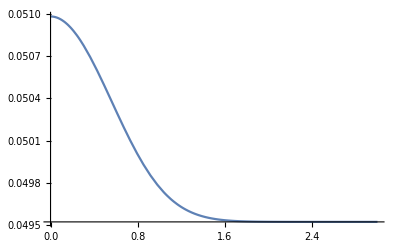

```mathematica
((x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)/.{λbar->1.093,x->1-α*Exp[-σ*r^2]})//Simplify
Plot[%/.{α->0.1,σ->1},{r,0,3}]
```

1/12-y^3/3+(-(√2)/9+(2 √2 y^2)/3-(8 √2 y^3)/9) √ϵ

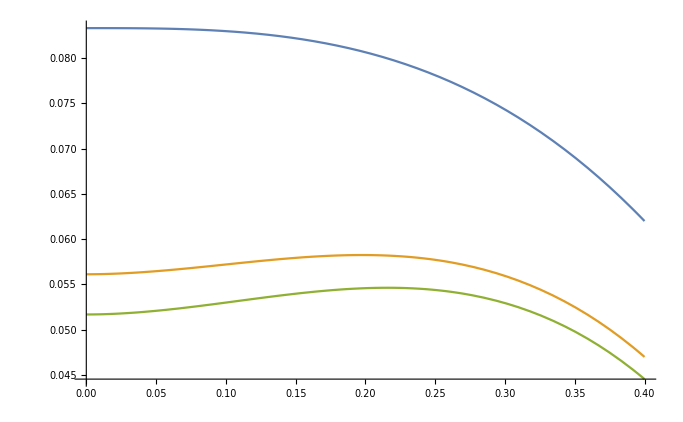

```mathematica
1/12-y^3/3+(-(√2)/9+(2 √2 y^2)/3-(8 √2 y^3)/9) √ϵ
Plot[{%/.ϵ->0,%/.ϵ->0.03,(%/.ϵ->0.03)-0.0044444444444444444+0.026666666666666665 y^2-0.035555555555555556 y^3},{y,0,0.4}]
```

```mathematica
D[1/108 x^2 (54-72 x+27 x^2)+1/108 x^2 (-48 √2 x+36 √2 x^2) √ϵ,x]//Simplify
Solve[%==0,x]
```

1/3 (-1+x) x (-3+x (3+4 √2 √ϵ))

{{x→0},{x→1},{x→3/(3+4 √2 √ϵ)}}

```mathematica
3/(3+4 √2 √ϵ)/.ϵ->0.001
```

0.943727

```mathematica
1.125-0.001
```

1.124

1/108 x^2 (54-72 x+27 x^2)+1/108 x^2 (-48 √2 x+36 √2 x^2) √ϵ

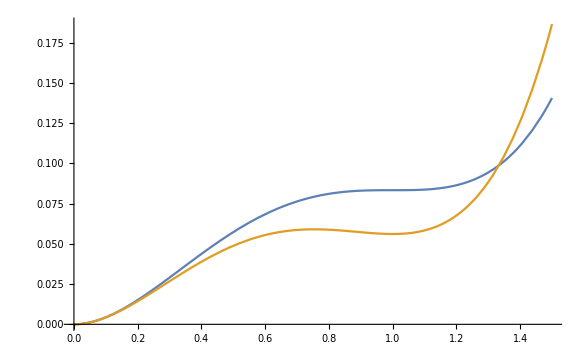

```mathematica
1/108 x^2 (54-72 x+27 x^2)+1/108 x^2 (-48 √2 x+36 √2 x^2) √ϵ
Plot[{%/.ϵ->0,%/.ϵ->0.03},{x,0,1.5}]
```

```mathematica
-
```

```mathematica
dePrivFn[dimlessV,x,λbar]
Normal@Series[%,{x,1,3}]
```

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

((-1+x)^2 (9+3 √(9-8 λbar)-8 λbar))/(8 λbar)+((-1+x)^3 (3+√(9-8 λbar)-2 λbar))/(2 λbar)+(-3-√(9-8 λbar)+4 λbar)/(16 λbar)

```mathematica
9/8-1.0921978114431945
```

0.0328022

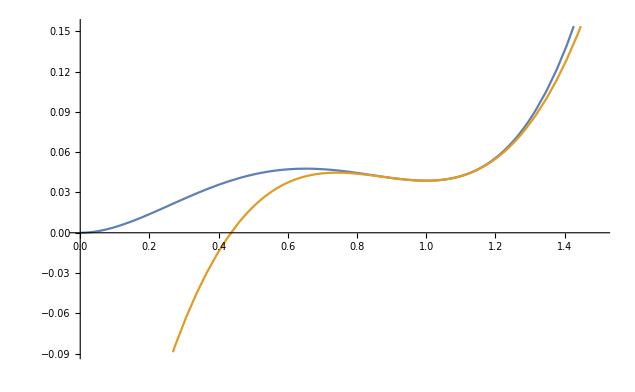

```mathematica
lbar=9/8-0.05;
dePrivFn[dimlessV,x,lbar];
Normal@Series[%,{x,1,3}];
Plot[{%%,%},{x,0,1.5}]
Clear[lbar]
```

### 1PT: quantities at (or near) critical temperature

#### S_E, T_PT, & β̄ in TWA

S_E=Σ/(θ-1)^2,
Γ/𝒱=(T^4(S_E/(2π)))^(3/2)e^-S_E,
 β̄=(d ln (Γ/𝒱))/(d ln T)≈(2Σ)/(θ-1)^3=±(2 S_E^(3/2))/(√Σ).

```mathematica
SE=Σ/(θ-1)^2;
GV=Tc^4 θ^4(SE/(2π))^(3/2)Exp[-SE];
βbar=Normal@Series[θ*D[Log[GV],θ],{θ,1,-3}];

SE
GV
βbar

Clear[SE,GV,βbar]
```

Σ/(-1+θ)^2

(ⅇ^(-Σ/(-1+θ)^2) Tc^4 θ^4 (Σ/(-1+θ)^2)^(3/2))/(2 √2 π^(3/2))

(2 Σ)/(-1+θ)^3

We assume that we can express the 1PT completion condition in terms of β, i.e. that the 1PT is relatively fast and we can use the saddle point approximation. Then:

(8π v_w^3 Γ/𝒱)/β^4=1, with β≡H_dec L_r β̄.

In the TWA:

(8π v_w^3×(T_c^4(S_E/(2π)))^(3/2)e^-S_E)/(H_dec^4(L_(r.c)^4(2/(√Σ)S_E^(3/2)))^4)=1.

⇒((v_w^3 Σ^2 T_c^4)/(4 √(2π)H_dec^4 L_(r,c)^4))S_E^(-9/2)e^-S_E≈1. 

Defining S'≡2/9 S_E:

⇒S' e^S'=(4/19683×(v_w^3 Σ^2 T_c^4)/(√π H_dec^4 L_(r,c)^4))^(2/9)=((√2)/(9(9π)^(1/8))(v_w^(3/4)T_c Σ^(1/2))/(H_dec|L_(r,c)|))^(8/9)≡e^(8/9 k)≡K

⇒S'=W(K): the Lambert-W (ProductLog) function

```mathematica
(8π vw^3 Tc^4(S/(2π))^(3/2)E^-S)/(Hd^4 LR^4(2/(√Σ)S^(3/2))^4)//Simplify
%/.S->9/2 Sp
Assuming[vw>0&&Σ>0&&Tc>0&&LR>0&&Hd>0&&Sp>0,(%^(2/9))//FullSimplify]
Solve[%==1,Sp]//Flatten
```

(ⅇ^-S Tc^4 vw^3 Σ^2)/(4 Hd^4 LR^4 √(2 π) S^(9/2))

(4 ⅇ^(-9 Sp/2) Tc^4 vw^3 Σ^2)/(19683 Hd^4 LR^4 √π Sp^(9/2))

(2^(4/9) ⅇ^-Sp vw^(2/3) ((Tc^8 Σ^4)/(Hd^8 LR^8))^(1/9))/(9 π^(1/9) Sp)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{Sp→ProductLog[(2^(4/9) vw^(2/3) ((Tc^8 Σ^4)/(Hd^8 LR^8))^(1/9))/(9 π^(1/9))]}

The Lambert-W function scales like W(K)≈ln(K) for large K:

S'=2/9 S_E≈ln(K)=8/9 k=8/9 ln((√2)/(9(9π)^(1/8))(v_w^(3/4)T_c Σ^(1/2))/(H_dec|L_(r,c)|))

⇒S_E≈4k=4ln((√2)/(9(9π)^(1/8))(v_w^(3/4)T_c Σ^(1/2))/(H_dec|L_(r,c)|))

θ=1±√(Σ/S_E)=1±√(Σ/(4k))
β̄=±(2 S_E^(3/2))/(√Σ)=±16/(√Σ)k^(3/2)

```mathematica
kPT=Log[(√2)/(9(9π)^(1/8))*(vw^(3/4)Tc √Σ)/(Hd*LR)];

temp={(List@@(Collect[LrcVals["γ<<1"]⟦1⟧,γ]))⟦-1⟧,LrcVals["γ<<1"]⟦2⟧}(*taking only the leading term of Subscript[L, r,c1]*);
kcVals["γ<<1"]=(kPT/.{Hd->HdecFactor,LR->Abs[#]//Simplify})&/@temp;
kcVals["γ>>1"]=(kPT/.{Hd->HdecFactor,LR->Abs[#]//Simplify})&/@LrcVals["γ>>1"];

Clear[temp]
```

```mathematica
SPT=4k;
θPT[dir_]:=1+Which[dir==="hot",√(Σ/SPT),dir==="cold",-√(Σ/SPT)];
βb[dir_]:=Which[dir==="hot",(2 SPT^(3/2))/(√Σ),dir==="cold",-(2 SPT^(3/2))/(√Σ)];
```

#### β_*≈β_PT

The approximate formula for β_PT in the TWA is

β_PT≈H_dec L_(r,c)β̄,

where:

β̄≈±(2 S_E^(3/2))/(√Σ)=±(16 k^(3/2))/(√Σ)=±16/(√Σ)(ln((√2)/(9(9π)^(1/8))(v_w^(3/4)T_c Σ^(1/2))/(H_dec|L_(r,c)|)))^(3/2).

```mathematica
temp={(List@@(Collect[LrcVals["γ<<1"]⟦1⟧,γ]))⟦-1⟧,LrcVals["γ<<1"]⟦2⟧}(*taking only the leading term of Subscript[L, r,c1]*);

βPrefVals["γ<<1"]=(HdecFactor*temp)//Simplify;
βPrefVals["γ>>1"]=(HdecFactor*LrcVals["γ>>1"])//Simplify;

BetaBar=(Abs[βb["hot"]]//Simplify)(*absolute value is the same for "hot" and "cold"*);

βAbsVals["γ<<1"]=(Abs[#]&/@βPrefVals["γ<<1"])*BetaBar//Simplify;
βAbsVals["γ>>1"]=(Abs[#]&/@βPrefVals["γ>>1"])*BetaBar//Simplify;

Clear[temp,BetaBar]
```

#### α_n≡(|ΔV|)/ρ_r

α_n=(|ΔV|)/ρ_r=(|ΔV|)/(A_ρ T_c^4):

```mathematica
Assuming[dePrivFn[cond1,μ,A,λ]&&θ>1,((dePrivFn[ΔV]/.dePrivFn[newdefs])/.T->θ*Tc)//Simplify];
Normal@Series[%,{θ,1,1}]
(%/(Arho Tc^4))/.{θ->1+ϵ}
```

-(16 Tc^4 (-1+θ) (4 A^4-3 A^2 λ μ^2))/(3 λ^3)

-(16 ϵ (4 A^4-3 A^2 λ μ^2))/(3 Arho λ^3)

```mathematica
ϵ=Abs[θPT["hot"]-1]//Simplify(*same both for "hot" and "cold"*);
αncVal=16/Arho*ϵ*(A^2 μ^2)/λ^2(1-4/3 A^2/(λ μ^2))
Clear[ϵ]
((%%/.Σ->Σfac)/.ARule)//FullSimplify
```

(8 A^2 (1-(4 A^2)/(3 λ μ^2)) μ^2 √(Σ/k))/(Arho λ^2)

(4 k √((2 π)/3) Δ^(9/4) μ^(9/2))/(Arho (k λ)^(3/2))

#### α_∞≡((χ_b/T)^2 μ^2/2)/A_ρ

```mathematica
Assuming[dePrivFn[cond1,μ,A,λ]&&θ>1,((dePrivFn[Xb]/.dePrivFn[potCoeffs])/.T->θ*Tc)//Simplify];
Normal@Series[%^2,{θ,1,0}]
(%/Tc^2)*μ^2/(2 Arho)
α∞Val=%;
%/.ARule
```

(16 A^2 Tc^2)/λ^2

(8 A^2 μ^2)/(Arho λ^2)

(6 Δ μ^4)/(Arho λ)

#### R^2≡((1+α)/(1+r_ϕ/r_r))^2=(r_r/(r_r+r_ϕ))^2(1+α)^2

For γ<<1, both x_(c,1/2) occur during ϕD, for γ>>1 x_c1 occurs during ϕD and x_c2 during RD.

R_c^2≈(r_dom)^-2(r_(r,c)^2(1+α))^2

```mathematica
R2cVals["γ<<1"]=({(1/1)^2,(1/(25/4*1/(f^8 γ^2)))^2}rrc^2(1+alpha)^2)//FullSimplify;
R2cVals["γ>>1"]=({(1/1)^2,(1/rrc)^2}rrc^2(1+alpha)^2)//FullSimplify;
```

#### a_*^4≈a_PT^4≈a_c^4

The formula is
a_c=exp[-N_mc](G^-1(g_0/g_IR))^(1/3)(T_0/T'_m),
where G is a ratio of DS and VS d.o.f. depending on how the VS was reheated from the DS, g_0 is the VS d.o.f. today, g_IR is the VS d.o.f. when it was reheated, T_0 the VS temperature today, T'_m an arbitrary DS temperature during DS RD at a time x_m, and N_mc the number of e-folds between x_c and x_m.

If x_c occurs during ϕD we pick x_m=x_eq, if it occurs during RD we pick x_m=x_c. Then:

ϕD: exp[-N_mc]=a_c/a_eq≈(r_eq/(r_(ϕ,c)))^(1/3)
RD: exp[-N_mc]=a_c/a_c=1

Defining G_fac=(G^-1(g_0/g_IR))^(1/3) and noting that T'_m=r_m^(1/4)f T_c:

ϕD: a_c^4=(r_eq/(r_(ϕ,c)))^(4/3)r_eq^-1 f^-4(G_fac^4(T_0/T_c))^4=r_eq^(1/3)r_(ϕ,c)^(-4/3)f^-4 (G_fac^4(T_0/T_c))^4
RD: a_c^4=r_c^-1 f^-4(G_fac^4(T_0/T_c))^4=(G_fac^4(T_0/T_c))^4

```mathematica
?rEq
```

```mathematica
ac4Vals["γ<<1"]=(rEq["γ<<1"]^(1/3)f^-4 Gfac^4(T0/Tc)^4{1^(-4/3),(25/4*1/(f^8 γ^2))^(-4/3)})//Simplify;
(List@@Collect[rEq["γ>>1"],γ])⟦1⟧;
ac4Vals["γ>>1"]={%^(1/3)f^-4 Gfac^4(T0/Tc)^4 1^(-4/3),Gfac^4(T0/Tc)^4};
```

#### Final recap

```mathematica
?kPT
```

```mathematica
?SPT
```

```mathematica
?θPT
```

```mathematica
?βb
```

```mathematica
?kcVals
```

```mathematica
?βPrefVals
```

```mathematica
?βAbsVals
```

```mathematica
?αncVal
```

```mathematica
?α∞Val
```

```mathematica
?R2cVals
```

```mathematica
?ac4Vals
```

### SGWB: approximate expressions for the amplitude and peak frequency

The amplitude of the envelope SGWB today is given by:

Ω_0^env≈(P_c(H_c/β))^2 F(v_w,f),

with F(v_w,f) the spectral function of the SGWB, and:

P_c≡(a_c^4(H_c/H_0))^4 R_c^2 ((α_n-α_∞)/α_n)^2 (α_n/(1+α_n))^2.

We will assume (as we have seen it is often the case) that |α_∞| >>α_n.

Therefore, the prefactors are:

```mathematica
PfacVals["γ<<1"]=(ac4Vals[#]*(HcVals[#]/Hnow)^2 R2cVals[#]((α∞Val)/alpha)^2(alpha/(1+alpha))^2&@"γ<<1")/.{Hnow->ρc^(1/2)/(√3 mPL)}
PfacVals["γ>>1"]=(ac4Vals[#]*(HcVals[#]/Hnow)^2 R2cVals[#]((α∞Val)/alpha)^2(alpha/(1+alpha))^2&@"γ>>1")/.{Hnow->ρc^(1/2)/(√3 mPL)}

(*checking some numbers*)
%%/.{ρc->ρcrit,T0->Tγ0,Arho->Aρ,Gfac->(gstar/gSM)^(-1/4)(gs0/gSM)^(1/3)}
%%/.{ρc->ρcrit,T0->Tγ0,Arho->Aρ,Gfac->(gstar/gSM)^(-1/4)(gs0/gSM)^(1/3)}
```

{(64 (22/3)^(1/3) A^4 Gfac^4 T0^4 γ^(2/3) μ^4)/(5^(2/3) Arho f^8 λ^4 ρc),(2048 (11/15)^(1/3) A^4 f^(32/3) Gfac^4 T0^4 γ^(16/3) μ^4)/(3125 Arho λ^4 ρc)}

{(32 2^(2/3) A^4 Gfac^4 T0^4 μ^4)/(Arho f^8 λ^4 ρc),(64 A^4 Gfac^4 T0^4 μ^4)/(Arho λ^4 ρc)}

{(0.0154732 A^4 γ^(2/3) μ^4)/(f^8 gstar^2 λ^4),(0.000215044 A^4 f^(32/3) γ^(16/3) μ^4)/(gstar^2 λ^4)}

{(0.0184835 A^4 μ^4)/(f^8 gstar^2 λ^4),(0.0232877 A^4 μ^4)/(gstar^2 λ^4)}

The ratios (H_c/β)^2 are:

```mathematica
(HcVals[#]/βAbsVals[#]&@"γ<<1")^2
(HcVals[#]/βAbsVals[#]&@"γ>>1")^2
```

{Σ/(16 f^8 k^3 γ^2),Σ/(36 k^3)}

{Σ/(16 f^8 k^3 γ^2),Σ/(256 k^3)}

Therefore, the SGWB amplitude today Ω_0 (writing Σ in terms of the parameters of the potential) is approximately given by:

```mathematica
Ω0Vals["γ<<1"]=(((PfacVals["γ<<1"]*(HcVals["γ<<1"]/βAbsVals["γ<<1"])^2)/.Σ->Σfac)/.ARule)//FullSimplify
Ω0Vals["γ>>1"]=(((PfacVals["γ>>1"]*(HcVals["γ>>1"]/βAbsVals["γ>>1"])^2)/.Σ->Σfac)/.ARule)//FullSimplify

(*comparing amplitudes from Subscript[x, c2] and Subscript[x, c1]:*)
Ω0Vals["γ<<1"]⟦2⟧/Ω0Vals["γ<<1"]⟦1⟧//N
Ω0Vals["γ>>1"]⟦2⟧/Ω0Vals["γ>>1"]⟦1⟧//N

(*plugging some numbers*)
Ω0Vals["γ<<1"]/.{ρc->ρcrit,T0->Tγ0,Arho->Aρ,Gfac->(gstar/gSM)^(-1/4)(gs0/gSM)^(1/3)}
Ω0Vals["γ>>1"]/.{ρc->ρcrit,T0->Tγ0,Arho->Aρ,Gfac->(gstar/gSM)^(-1/4)(gs0/gSM)^(1/3)}
```

{(2 (22/3)^(1/3) Gfac^4 π T0^4 Δ^(9/2) μ^9)/(3 5^(2/3) Arho f^16 k^3 γ^(4/3) (-1+Δ)^2 λ^3 ρc),(256 (11/15)^(1/3) f^(32/3) Gfac^4 π T0^4 γ^(16/3) Δ^(9/2) μ^9)/(84375 Arho k^3 (-1+Δ)^2 λ^3 ρc)}

{(2^(2/3) Gfac^4 π T0^4 Δ^(9/2) μ^9)/(3 Arho f^16 k^3 γ^2 (-1+Δ)^2 λ^3 ρc),(Gfac^4 π T0^4 Δ^(9/2) μ^9)/(24 Arho k^3 (-1+Δ)^2 λ^3 ρc)}

0.00617681 f^(80/3) γ^(20/3)

0.0787451 f^16 γ^2

{(0.00050636 Δ^(9/2) μ^9)/(f^16 gstar^2 k^3 γ^(4/3) (-1+Δ)^2 λ^3),(3.12769×10^-6 f^(32/3) γ^(16/3) Δ^(9/2) μ^9)/(gstar^2 k^3 (-1+Δ)^2 λ^3)}

{(0.00060487 Δ^(9/2) μ^9)/(f^16 gstar^2 k^3 γ^2 (-1+Δ)^2 λ^3),(0.0000476306 Δ^(9/2) μ^9)/(gstar^2 k^3 (-1+Δ)^2 λ^3)}

The peak frequency is:

```mathematica
f0pkVals["γ<<1"]=(Assuming[Gfac>0,(ac4Vals["γ<<1"]^(1/4)//Simplify)]*βAbsVals["γ<<1"]/.{Σ->(Σfac/.ARule)})//Simplify
f0pkVals["γ>>1"]=(Assuming[Gfac>0,(ac4Vals["γ>>1"]^(1/4)//Simplify)]*βAbsVals["γ>>1"]/.{Σ->(Σfac/.ARule)})//Simplify

(*comparing frequencies from Subscript[x, c2] and Subscript[x, c1]:*)
(f0pkVals["γ<<1"]⟦2⟧/f0pkVals["γ<<1"]⟦1⟧)//Simplify//N
(f0pkVals["γ>>1"]⟦2⟧/f0pkVals["γ>>1"]⟦1⟧)//Simplify//N

(*plugging some numbers, and writing it in mHz*)
f0pkVals["γ<<1"]*GeV/mHz/.{ρc->ρcrit,T0->Tγ0,Arho->Aρ,mPL->mpl,Tc->1GeV*Tc,Gfac->(gstar/gSM)^(-1/4)(gs0/gSM)^(1/3)}
f0pkVals["γ>>1"]*GeV/mHz/.{ρc->ρcrit,T0->Tγ0,Arho->Aρ,mPL->mpl,Tc->1GeV*Tc,Gfac->(gstar/gSM)^(-1/4)(gs0/gSM)^(1/3)}
```

{(2^(7/12) 3^(11/12) 11^(1/12) f^5 Gfac T0 Tc γ^(7/6) √((Arho k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/(5^(1/6) mPL √π),(3 3^(11/12) 5^(1/6) 11^(1/12) Gfac T0 Tc √((Arho k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/(2^(3/4) f^(1/3) mPL √π γ^(1/6))}

{(3 2^(5/12) f^5 Gfac T0 Tc γ √((Arho k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/(mPL √π),(12 Gfac √(2/π) T0 Tc √((Arho k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/mPL}

2.03581/(f^(16/3) γ^(4/3))

4.23785/(f^5 γ)

{(0.000198616 f^5 Tc γ^(7/6) √((gstar k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/gstar^(1/4),(0.000404345 Tc √((gstar k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/(f^(1/3) gstar^(1/4) γ^(1/6))}

{(0.000207642 f^5 Tc γ √((gstar k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/gstar^(1/4),(0.000879955 Tc √((gstar k^3 (-1+Δ)^2 λ)/(Δ^(5/2) μ)))/gstar^(1/4)}

k as a function of the parameters:

```mathematica
?kcVals
```

Since (Ω_(0,2))/(Ω_(0,1))>1 (as can be seen by plugging in the smallest f_min≈1.6/γ^(1/4) for γ<<1, and f≈1 for γ>>1), we want the 1PT to complete during x_c2. Let us then focus on the second entry (i.e. x_c2) of these lists.

Plugging in some typical numbers:

```mathematica
VALS1={mPL->mpl,vw->1,ρc->ρcrit,T0->Tγ0,Arho->Aρ,Gfac->(gstar/gSM)^(-1/4)(gs0/gSM)^(1/3),Tc->1GeV*Tc};
VALS2={gstar->10,f->(1.6/γ^(1/4)),Δ->0.5,μ->2,λ->0.5,Tc->10^3};
VALS3={γ->0.05};



Print["Ω_0:"]
((Ω0Vals["γ<<1"]⟦2⟧/.{k->(kcVals["γ<<1"]⟦2⟧/.Σ->1)})/.VALS1);
(%/.VALS2)/.VALS3

Print["f_(0, pk) [mHz]:"]
((f0pkVals["γ<<1"]⟦2⟧/.{k->(kcVals["γ<<1"]⟦2⟧/.Σ->1)})/.VALS1);
(GeV/mHz%/.VALS2)/.VALS3

Clear[VALS1,VALS2,VALS3]
```

Ω_0:

3.32952×10^-11

f_(0, pk) [mHz]:

87.4189

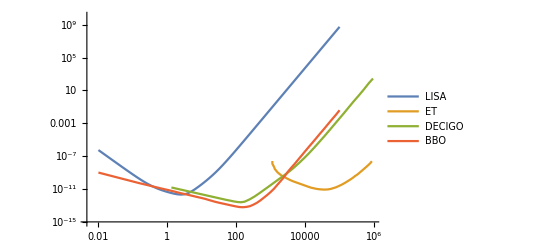

```mathematica
ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotLegends->{"LISA","ET","DECIGO","BBO"},PlotRange->{10^-15,10^10}]
```

## SGWB

### SGWB spectra formulas

```mathematica
Clear[fenv,Senvf,Ωenv,fsw,Sswf,Ωsw,fturb,fturb,Sturbf,Ωturb,κFn]

(*GW from envelope approximation*)
fenv[β_,vw_]:=Abs[β](0.62/(1.8-0.1vw+vw^2))*GeV/mHz(*[mHz]*);
Senvf[f_,fenv_]:=(3.8 (f/fenv)^2.8)/(1+2.8(f/fenv)^3.8);
Ωenv[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*R^2((κ α)/(1+α))^2*(Hs/β)^2((0.11 vw^3)/(0.42+vw^2))Senvf[f,Z^-1 fenv[β,vw]];

(*GW from sound waves*)
fsw[β_,vw_]:=2/(√3)×β/vw*GeV/mHz(*[mHz]*);
Sswf[f_,fsw_]:=(f/fsw)^3(7/(4+3(f/fsw)^2))^(7/2)
Ωsw[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*0.159*R^2((κ α)/(1+α))^2*(Hs/β)vw Sswf[f,Z^-1 fsw[β,vw]];

(*GW from turbulence*)
fturb[β_,vw_]:=3.5/2×β/vw*GeV/mHz(*[mHz]*);
Sturbf[f_,fturb_,hstar_]:=(f/fturb)^3/((1+f/fturb)^(11/3)(1+8π f/hstar))
Ωturb[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*20.1*R^2((κ α)/(1+α))^2*(Hs/β)vw Sturbf[f,Z^-1 fturb[β,vw],Z^-1 Hs*GeV/mHz];

(*efficiency*)
κFn[vw_,αN_]:=Block[{αn=αN,αmax,α,cs,vwJ,κA,κB,κC,κD,δκ},

αmax=1/3(1-vw)^(-13/10);
α=Min[αN,αmax];
cs=√(1/3);
vwJ=1/(1+α)(√(2/3 α+α^2)+√(1/3));
κA=vw^(6/5)(6.9α)/(1.36-0.037 √α+α);
κB=α^(2/5)/(0.017+(0.997+α)^(2/5));
κC=(√α)/(0.135+√(0.98+α));
κD=α/(0.73+0.083 √α+α);
δκ=-0.9Log[(√α)/(1+√α)];

If[0≤vw≤cs,
(cs^(11/5)κA κB)/((cs^(11/5)-vw^(11/5))κB+vw cs^(6/5)κA),
If[cs<vw<vwJ,
κB+(vw-cs)δκ+(vw-cs)^3/(vwJ-cs)^3(κC-κB-(vw-cs)δκ),
If[vwJ≤vw≤1,
((vwJ-1)^3 vwJ^(5/2)vw^(-5/2)κC κD)/(((vwJ-1)^3-(vw-1)^3)vwJ^(5/2)κC+(vw-1)^3 κD),
Print["Error"]
]
]
]
];
```

### SGWB from 1PT

```mathematica
Clear[gwSpectra]

gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γϕ_,method_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwf_List:{Automatic,0,gSM,True,0},δxLargePrecAccu_List:{10^-6,10^3,30,20}]:=gwSpectra[gUVs,vwCool,coeffs,Tcrit,Hd,Γϕ,method,verbose,hh,KfacΓfull,NlxExpansionSum,IRinstantVSRHwf,δxLargePrecAccu]=Block[{gdUV,gUV,gstar,Tc=Tcrit,Hi=Hd,γd=Γϕ/Hd,Kfactor,full,Nlx,expansion,sum,wϕ,gdIR,gd0,gIR,instantVSRH,δ,xLarge,prec,accu,xd,t0,rϕ,rr,Tx,ax,tx,xDomain,xm,rCrit,xCritBoil,xpk,xCritCool,Tpk,xcs,tcs,TempEvol,gammas,vwboil=1,Tpts,tpts,λbars,χbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs,xpts,Hss,Rs,Zs, fullResult,fullResultLabels,spec},

(*distributing list arguments*)
{gdUV,gUV}=gUVs(*DS & VS UV d.o.f.*);
gstar=gdUV+gUV(*total plasma UV d.o.f.*);

{Kfactor,full}=KfacΓfull(*K-prefactor for Subscript[Γ, nucl]/𝒱; whether (Subscript[S, E]/2π)^(3/2) 0-modes prefactor included*);

{Nlx,expansion,sum}=NlxExpansionSum(* # ln(x) steps; whether Universe expansion considered; whether sum for a(x) and τ̄(x) considered*);

{gdIR,gd0,gIR,instantVSRH,wϕ}=IRinstantVSRHwf(*DS d.o.f. in IR; DS-to-VS temperature ratio in IR; VS d.o.f. in IR, VS temperature in IR; whether VS reheated instantaneously; reheaton e.o.s.*);
gdIR=If[gdIR===Automatic,gdUV,gdIR];

{δ,xLarge,prec,accu}=δxLargePrecAccu(*tiny number for derivative computation, largest x-value for reheating story, precision, accuracy*);

(*the reference time, at which the ϕ-decays start*)
xd=(2/3)/(1+wϕ);
t0=xd/Hi;

(*the solutions to the reheating equations*)
{rϕ,rr}=solEqs[γd,wϕ,xLarge,prec,accu];

(*T(x)*)
Tx=TOfx[γd,gstar,Hi,wϕ,xLarge,prec,accu];

(*scale factor a(x), with Subscript[a, ini]=a(x=2/3)=1*)
ax=If[expansion==False,1,aOfx[γd,1,sum,wϕ,xLarge,prec,accu]];

(*dimensionless comoving time τ̄(x)*)
tx=If[expansion==False,1,tauOfx[γd,1,1,sum,wϕ,xLarge,prec,accu]];

(*its time domain*)
xDomain=(InterpolatingFunctionDomain[Tx]//Flatten);

(*deep in DS RD*)
xm=xDomain⟦-1⟧;

(*the dimensionless radiation density at critical temperature*)
rCrit=(Aρ Tc^4)/ρϕi;

(*the dimensionless crossing times, at which the radiation density reaches critical temperature*)
{xCritBoil,xpk,xCritCool}=xCross[γd,rCrit,wϕ,xLarge,prec,accu];

(*the peak temperature*)
Tpk=Tx[xpk];

(*a handy list for dimensionless crossing times*)
xcs={xCritBoil,xCritCool};

(*the dimensionful critical times*)
tcs=xcs/Hi;

(*reading 'method' argument to find PT temperature*)
If[MemberQ[{"analytic","semi","numeric","alt"},method]==False,Return["Please write argument 'method' a string: either 'analytic', 'semi', 'numeric', or 'alt'."]];

(*computing the PT*)
If[method=="analytic",
(*the power law behavior of the temperature as a function of time*)
gammas=gammaRate[γd,#,wϕ,δ,xLarge,prec,accu]&/@xcs;
(*the parameters for the temperature evolution*)
TempEvol=Table[{gammas⟦i⟧,t0,tcs⟦i⟧},{i,2}];
,
(*the arguments for the temperature evolution*)
TempEvol={Tx,1/Hi}&/@{_,_}(*making a copy: for boiling and cooling*);
];

(*finding the properties of the phase transition: a list of pairs; the first entry being the boiling PT, the second the cooling PT*)
(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[χ, b], ϵ, Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], Subscript[α, n], Subscript[κ, run]}*)
{Tpts,tpts,λbars,χbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs}={CheckAbort[ptParams[gstar,"hot",vwboil,TempEvol⟦1⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]],
CheckAbort[ptParams[gstar,"cold",vwCool,TempEvol⟦2⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]]}//Transpose;

(*dimensionless times at which the PT took place*)
xpts=tpts*Hi;

(*Hubble scale at the time of GW generation, which we take to be the time of the PT: H_*=Subscript[H, PT]*)
Hss=Hi*√(rϕ[#]+rr[#])&/@xpts;

(*correction due to Subscript[ρ, tot] containing a contribution from the reheaton and not only the DS radiation*)
Rs=Table[((1+αns⟦i⟧)/(1+rϕ[xpts⟦i⟧]/rr[xpts⟦i⟧])),{i,2}];

(*the extra redshift factor that GW from boiling PT undergo compared to those from cooling PT*)
Zs=redshift[γd,Hi,{#,xm},{gdUV,gUV},{gdIR,gd0,gIR},instantVSRH,wϕ,xLarge,prec,accu,False]&/@xpts;

fullResult={xpk/Hi,xpk,Tpk,tcs,xcs,Tpts,tpts,tpts*Hi,λbars,χbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs,Hss,Rs,Zs};
fullResultLabels={"t_max=``","x_max=``","T_max=``","t_c=``","x_c=``","T_PT=``","t_PT=``","x_PT=``","λ̄=``","χ_b=``","ϵ=``","E_c=``","S_E=``","S_E'=``","S_E''=``","Γ/V=``","β_1=``","β_2=``","n_b=``","R_b=``","⟨R⟩=``","β_eff=``","α_∞=``","α_n=``","κ_eff=``","H_*=``","R=``","Z=``"};

(*print the quantities above*)
If[verbose,Print[StringRiffle[Table[StringForm[fullResultLabels⟦i⟧,ScientificForm[fullResult⟦i⟧,4]],{i,Length@fullResult}],"\n"]]];

spec={Ωenv[f,βeffs⟦1⟧,vwboil,Rs⟦1⟧,effs⟦1⟧,αns⟦1⟧,Hss⟦1⟧,Zs⟦1⟧,hh],Ωsw[f,βeffs⟦2⟧,vwCool,Rs⟦2⟧,κFn[vwCool,αns⟦2⟧],αns⟦2⟧,Hss⟦2⟧,Zs⟦2⟧,hh]};

Return[spec]
]
```

### Examples

Some examples of parameters that work:

1. g_s=10, v_w^c=0.05, {μ, Δ, λ}={2,0.5, 1}, T_c=500 GeV (—5 TeV), γ=0.2, f=(1.03×1.7/γ^(1/4))
2. g_s=10, v_w^c=0.05, {μ, Δ, λ}={2,0.8, 1}, T_c=200 GeV, γ=0.2 (0.3), f=(1.3×1.7/γ^(1/4))
3. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1.1,0.90889, 1.1}, T_c=5 TeV, γ=0.3, f=(3.7×1.7/γ^(1/4))
4. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1.5,0.888789, 1}, T_c=5 TeV, γ=0.02, f=(2.2×1.7/γ^(1/4))
5. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1, 0.90889, 1}, T_c=500 GeV (—5 TeV), γ=50, f = 3.5*(1+1/γ^(1/2))

#### Parameters

{μ,A,λ}={1.5,1.22481,1}

T_c exists: True

γ=0.02, f=9.94521

T_c=1000 GeV

T_max=2279.74 GeV

T_s=0.-31412.8 ⅈ GeV

{x_c1,x_max,x_c2}={0.672,1.196,38.562}

λ̄(T_max)=1.10085 (if not smaller than 9/8=1.125 then T_s is reached)

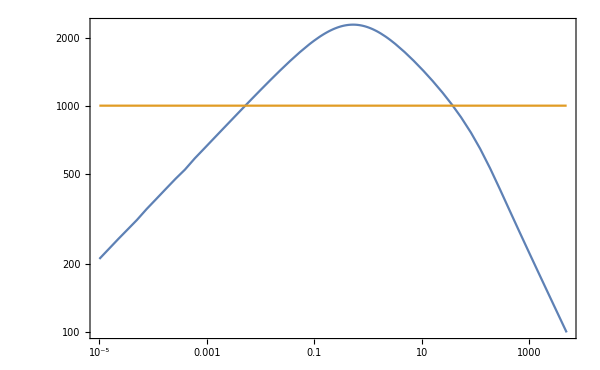

```mathematica
verbose=True;
gDSUV=10;
gVSUV=106.75(*DSRH & VSRH*);
gs=gDSUV+gVSUV;
vwc=0.05;

(*
(*VERY STRONG 1PT: Subscript[α, n]>1 ⇒ vacuum energy is important ⇒ evolution during RH is suspect*)
μ=10;
λ=3;*)
μ=1.5;
λ=1;
(*Δ=8/9+0.02;*)
Δ=8./9+0.0001;
(*Δ=0.95;*)
(*Δ=8/9-0.0001;*)
(*Δ=0.89;*)
(*Δ=0.85;*)
A=(A/.(dePrivFn["PT",ARule]));
pars={μ,A,λ};
Print["{μ,A,λ}=",pars]
Print["T_c exists: ",dePrivFn["PT",cond1,pars⟦1⟧,pars⟦2⟧,pars⟦3⟧]]

Tcr=1000GeV;

gam=0.02;
regime=If[gam≤1,"γ<<1","γ>>1"];
(*Print["f∈[",((dePrivFn["RH",RHDict["fmin"][regime]])/.γ->gam)//N,", ",(fMax[regime]/.γ->gam)//N,"]"]*)
eff=If[regime=="γ<<1",2.2*(1.7/gam^(1/4)),3.3*(1+1./gam^(1/2))];
Print["γ=",gam,", f=",eff]

solEqs[gam];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);Gam=gam*Hdec;

Tofx=TOfx[Gam/Hdec,gs,Hdec];
dlnTdt[x_]=Hdec*D[Tofx[x],x]/Tofx[x];
d2lnTdt2[x_]=Hdec*D[dlnTdt[x],x];

domain=InterpolatingFunctionDomain[Tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=Tofx[xMAX];

Print["T_c=",Tcr, " GeV"]
Print["T_max=",Tmx," GeV"]
Print["T_s=",(Ts/.dePrivFn["PT",Tspinodal])/.Tc->Tcr, " GeV"]
Print["{x_c1,x_max,x_c2}=",Round[#,0.001]&/@{xC1,xMAX,xC2}]
Print["λ̄(T_max)=",(dePrivFn["PT",λbar]/.dePrivFn["PT",McλbarToCoeffs])/.{Tc->Tcr,T->Tmx}," (if not smaller than 9/8=1.125 then T_s is reached)"]


LogLogPlot[{Tofx[2/3+dx],Tcr},{dx,10^-5,domain⟦-1⟧-2/3},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\mathrm{Temperature}\\ [\\mathrm{GeV}]",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["T_\\mathrm{rh}(x)",Magnification->1.7],MaTeX["T_\\mathrm{c}",Magnification->1.7]}],{0.9,0.85}]]
```

#### 1PT evolution

S_E(T_max)=127.409

S_E(T_max)/(4×ln[m_Pl/T_c])=0.927821

S_E''(T_max)=2.70681×10^-16

For supracritical 1PT:

w/o 0-modes: n_0 = 1.54778×10^-32,  (8π·n_0·v_w^3)^(1/3) = 7.29989×10^-11

w/ 0-modes: n_0 = 1.41332×10^-30,  (8π·n_0·v_w^3)^(1/3) = 3.28721×10^-10

General::munfl: Exp[-46630.5] is too small to represent as a normalized machine number; precision may be lost.

............

w/o 0-modes:

x_PT=33.713

T_PT=3131.2 GeV

n_b = 1.55583×10^-32,  β_eff = 7.31252×10^-11

............

w/ 0-modes:

x_PT=8.416

T_PT=4639.7 GeV

n_b = 1.42907×10^-30,  β_eff = 3.29937×10^-10

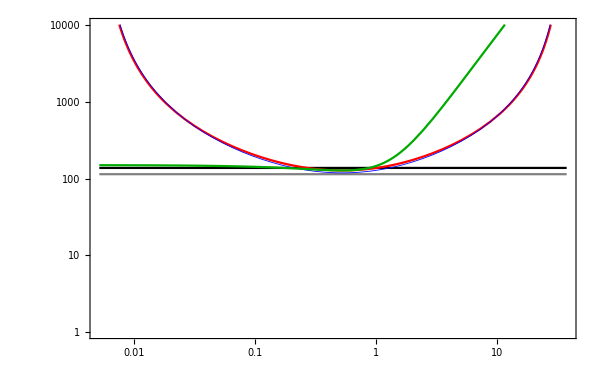

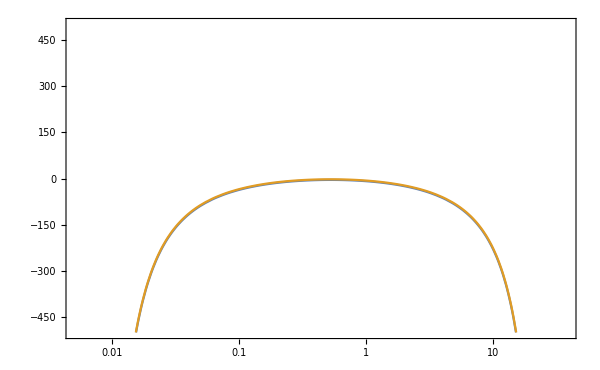

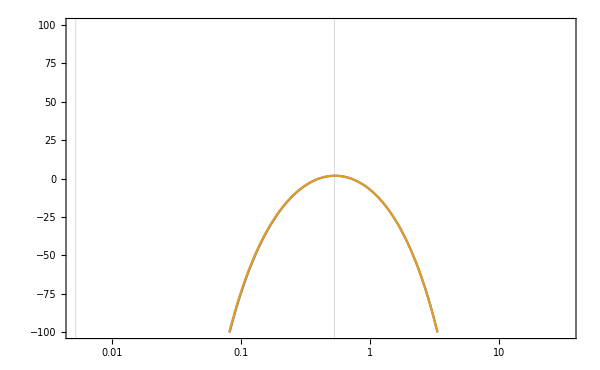

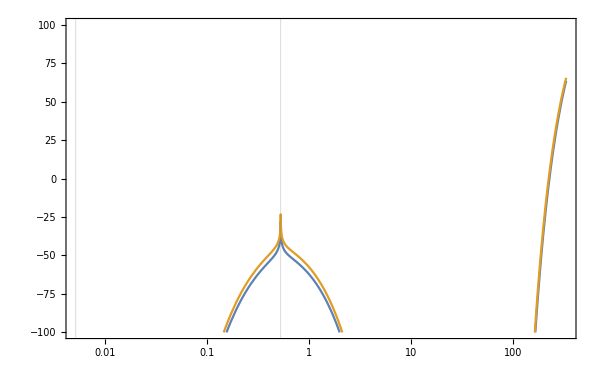

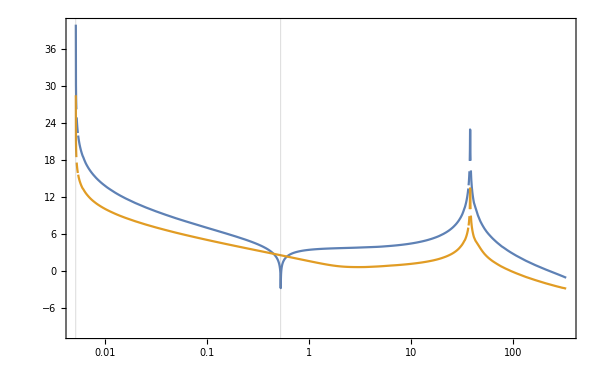

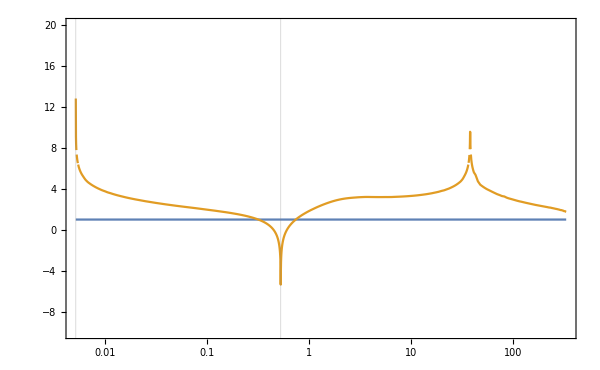

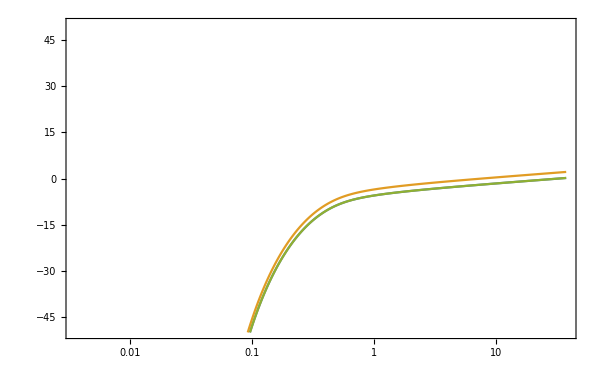

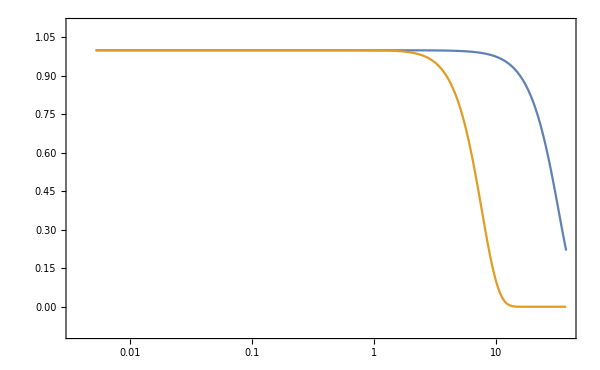

```mathematica
SE2Max=S2Rate[dlnTdt[xMAX],d2lnTdt2[xMAX],pars,Tcr,Tmx];

GV=(Γnucl[pars,Tcr,Tofx[xMAX],1,False]);
GV0m=(Γnucl[pars,Tcr,Tofx[xMAX],1,True]);
n0=(√(2π))/(√SE2Max)GV;
n00m=(√(2π))/(√SE2Max)GV0m;


(*Print["log_10(Γ/𝒱)_T_max=",Γnucl[pars,Tcr,Tmx,1,False,True]]*)
Print["S_E(T_max)=",SETemp[pars,Tcr,Tmx]]
Print["S_E(T_max)/(4×ln[m_Pl/T_c])=",SETemp[pars,Tcr,Tmx]/(4Log[mpl/Tcr])]
Print["S_E''(T_max)=",SE2Max]
Print["For supracritical 1PT:"]
Print["w/o 0-modes: n_0 = ",n0,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n0 1^3)^(1/3)]
Print["w/ 0-modes: n_0 = ",n00m,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n00m 1^3)^(1/3)]


{Tptn0,tptn0,λbarr,Xbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,False,{1,1},250];

Print["............"]
Print["w/o 0-modes:"]
Print["x_PT=",Round[tptn0*Hdec,0.001]]
Print["T_PT=",Tptn0," GeV"]
Print["n_b = ",nbub,",  β_eff = ",beff]

{Tptw0,tptw0,λbarr,Xbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,True,{1,1},250];

Print["............"]
Print["w/ 0-modes:"]
Print["x_PT=",Round[tptw0*Hdec,0.001]]
Print["T_PT=",Tptw0," GeV"]
Print["n_b = ",nbub,",  β_eff = ",beff]

Clear[λbarr,Xbb,epss,Ecr,SEu,SE1,SE2,GV,GV0m,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff]


LogLogPlot[{4Log[mpl/Tcr],4Log[Tcr/Hdec],SETemp[pars,Tcr,Tofx[2/3+dx]],approxSE/.{θ->(Tofx[2/3+dx]/Tcr)},SETemp[pars,Tcr,Tofx[xMAX]]+SE2Max*1/2((2/3+dx)-xMAX)^2*Hdec^-2},{dx,xC1-2/3,xC2-2/3},Frame->True,PlotRange->{1,10^4},PlotStyle->{Black,Gray,Red,{Blue,Thickness[0.001]},Darker@Green},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["S_\\mathrm{E}",Magnification->2]},PlotLabel->MaTeX["\\text{Euclidean Action}",Magnification->1.7],PlotLegends->Placed[LineLegend[{MaTeX["4 \\ln(m_\\mathrm{Pl}/T_\\mathrm{c})",Magnification->1],MaTeX["4 \\ln(T_\\mathrm{c}/H_\\mathrm{dec})",Magnification->1],MaTeX["S_E(x)",Magnification->1],MaTeX["S_E^\\mathrm{ appx.}(x)",Magnification->1],MaTeX["S_E^{\\prime\\prime}(t-t_\\mathrm{max})^2 /2",Magnification->1]}],{0.2,0.25}]]
(*Export[PlotsDir<>"SE_x.pdf",%]*)

LogLinearPlot[{Γnucl[pars,Tcr,Tofx[2/3+dx],1,False,True]-4Log10[Hdec],Γnucl[pars,Tcr,Tofx[2/3+dx],1,True,True]-4Log10[Hdec]},{dx,xC1-2/3,xC2-2/3},Frame->True,PlotRange->{-500,500},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H_\\mathrm{dec}^4)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.7],MaTeX["\\text{w/ 0-modes}",Magnification->1.7]}],{0.8,0.85}]]

LogLinearPlot[{Log[4/3 π*1^3(2/3+dx)((tptn0*Hdec)-(2/3+dx))^3]+Γnucl[pars,1,Tofx[2/3+dx]/Tcr,1,False,True]*Log[10]+4Log[Tcr/Hdec],Log[4/3 π*1^3(2/3+dx)((tptw0*Hdec)-(2/3+dx))^3]+Γnucl[pars,1,Tofx[2/3+dx]/Tcr,1,True,True]*Log[10]+4Log[Tcr/Hdec]},{dx,xC1-2/3,(Max[tptn0,tptw0]*Hdec)-2/3},Frame->True,PlotRange->{-100,100},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[J(x_{\\rm PT},x')]",Magnification->2]},PlotLabel->MaTeX["\\text{Origin of Bubbles}",Magnification->1.7],GridLines->{{(xC1-2/3)}~Join~{xMAX - 2/3},None}]

LogLinearPlot[{Log[8π*1^3]+Γnucl[pars,1,Tofx[2/3+dx]/Tcr,1,False,True]*Log[10]-4Log[Abs[S1Rate[dlnTdt[2/3+dx],pars,Tcr,Tofx[2/3+dx]]]],Log[8π*1^3]+Γnucl[pars,1,Tofx[2/3+dx]/Tcr,1,True,True]*Log[10]-4Log[Abs[S1Rate[dlnTdt[2/3+dx],pars,Tcr,Tofx[2/3+dx]]]]},{dx,xC1-2/3,10((Max[tptn0,tptw0]*Hdec)-2/3)},Frame->True,PlotRange->{-100,100},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\mathrm{cond}(x)]",Magnification->2]},PlotLabel->MaTeX["\\text{1PT condition}",Magnification->1.7],GridLines->{{(xC1-2/3)}~Join~{xMAX - 2/3},None}]

LogLinearPlot[{Log[Abs[S1Rate[dlnTdt[2/3+dx],pars,Tcr,Tofx[2/3+dx]]]/Hdec],Log[√Abs[S2Rate[dlnTdt[2/3+dx],d2lnTdt2[2/3+dx],pars,Tcr,Tofx[2/3+dx]]]/Hdec]},{dx,xC1-2/3,10((Max[tptn0,tptw0]*Hdec)-2/3)},Frame->True,PlotRange->{-10,40},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\vert S^(n)(x)\\vert^{1/n}]",Magnification->2]},PlotLabel->MaTeX["\\text{Action rates of change}",Magnification->1.7],GridLines->{{(xC1-2/3)}~Join~{xMAX - 2/3},None}]

LogLinearPlot[{1,Log[Abs[S1Rate[dlnTdt[2/3+dx],pars,Tcr,Tofx[2/3+dx]]]/√Abs[S2Rate[dlnTdt[2/3+dx],d2lnTdt2[2/3+dx],pars,Tcr,Tofx[2/3+dx]]]]},{dx,xC1-2/3,10((Max[tptn0,tptw0]*Hdec)-2/3)},Frame->True,PlotRange->{-10,20},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\vert S^(n)(x)\\vert^{1/n}]",Magnification->2]},PlotLabel->MaTeX["\\text{Action rates of change}",Magnification->1.7],GridLines->{{(xC1-2/3)}~Join~{xMAX - 2/3},None}]


(*h(x) w/o scale factor*)
Lmlnh1=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1},250];

(*Subscript[n, b](x) w/o scale factor*)
LnbLx=Lnbubble[Lmlnh1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1}];
xData=(InterpolatingFunctionCoordinates[LnbLx]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[LnbLx]//Flatten);
LnbLx={(10^xData)-2/3,10^yData}//Transpose;

xData=(InterpolatingFunctionCoordinates[Lmlnh1]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh1]//Flatten);
Lmlnh1={(10^xData)-2/3,yData}//Transpose;

Lmlnh2=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,True,{1,1},250];

xData=(InterpolatingFunctionCoordinates[Lmlnh2]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh2]//Flatten);
Lmlnh2={(10^xData)-2/3,yData}//Transpose;

Lmlnh3=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1},500];
xData=(InterpolatingFunctionCoordinates[Lmlnh3]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh3]//Flatten);
Lmlnh3={(10^xData)-2/3,yData}//Transpose;

ListLogLinearPlot[{Lmlnh1,Lmlnh2,Lmlnh3},Joined->True,PlotRange->{-50,50},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10} (-\\ln h(x))",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2],MaTeX["\\text{w/o 0-modes; more steps}",Magnification->1.2]}],{0.3,0.75}]]

Lmlnh1=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh2);

ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.2,0.15}],GridLines->{{xMAX - 2/3}~Join~{tptn0*Hdec - 2/3}~Join~{tptw0*Hdec - 2/3},{1/E}}]

Lmlnh1=({#⟦1⟧+2/3,#⟦2⟧}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧+2/3,#⟦2⟧}&/@Lmlnh2);

p1=ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["t H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.8,0.85}],GridLines->{{xMAX }~Join~{tptn0*Hdec}~Join~{tptw0*Hdec - 2/3},{1/E}}];
p2=LogLinearPlot[{Exp[-(4π)/3*(n0/Hdec^3)*1^3*(x-xMAX)^3],Exp[-(4π)/3*(n00m/Hdec^3)*1^3*(x-xMAX)^3]},{x,Lmlnh1⟦1,1⟧,Lmlnh1⟦-1,1⟧},PlotStyle->{Darker@Green,Red},PlotRange->{-0.1,1.1},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes; analytic, simultaneous}",Magnification->1.2],MaTeX["\\text{w 0-modes; analytic, simultaneous}",Magnification->1.2]}],{0.7,0.65}]];
Show[p1,p2]
```

#### SGWB

```mathematica
?gwSpectra
```

StringForm::string: String expected at position StandardForm[Short[Shallow[HoldForm[1], {10, 50}], 5]] in StandardForm[Short[Shallow[HoldForm[StringForm[fullResultLabels[[i]], ScientificForm[fullResult[[i]], 4]]], {10, 50}], 5]].

```mathematica
(*gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γϕ_,method_,verbose_:False,hh_:0.67,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwf_List:{Automatic,0,106.75,True,0},δxLargePrecAccu_List:{1/1000000,1000,30,20}]*)
```

```mathematica
?redshift
```

```mathematica
(*redshift[gam,gs,Hdec,{33.71,1000},True,{10,1,gSM,1000},0,1000,30,20,True]
redshift[gam,gs,Hdec,{33.71,1000},False,{10,1,gSM,1000},0,1000,30,20,True]

redshift[gam,gs,Hdec,{33.71,450},True,{10,1,gSM,1000},0,1000,30,20,True]
redshift[gam,gs,Hdec,{33.71,450},False,{10,1,gSM,1000},0,1000,30,20,True]*)
```

```mathematica
10/(7/4(4/11)^(4/3)*(gSM/gs0)^(4/3))
10/(7/4(4/11)^(4/3)*(200/gs0)^(4/3))
```

0.270547

0.117137

*****************

No 0-modes:

.................

t_max=8.228*10^9
x_max=1.196
T_max=2.28*10^3
t_c={4.623*10^9, 2.654*10^11}
x_c={6.719*10^-1, 3.856*10^1}
T_PT={1.532*10^3, 5.086*10^2}
t_PT={6.003*10^10, 1.404*10^12}
x_PT={8.724, 2.04*10^2}
λ̄={1.072, 6.421*10^-1}
χ_b={6.855*10^3, 3.093*10^3}
ϵ={8.737*10^12, 7.416*10^11}
E_c={7.513*10^5, 5.521*10^4}
S_E={4.904*10^2, 1.086*10^2}
S_E'={9.978*10^-9, -1.934*10^-10}
S_E''={1.524*10^-19, 4.068*10^-22}
Γ/V={5.931*10^-201, 4.797*10^-37}
β_1={-9.996*10^-9, 1.92*10^-10}
β_2={-1.521*10^-19, -4.059*10^-22}
n_b={1.729*10^-33, 1.324*10^-27}
R_b={8.332*10^10, 9.106*10^8}
⟨R⟩={5.541*10^10, 5.691*10^10}
β_eff={3.515*10^-11, 1.608*10^-10}
α_∞={-5.864*10^-1, 1.083}
α_n={4.128*10^-2, 2.886*10^-1}
κ_eff={1.52*10^1, -2.754}
H_*={1.093*10^-11, 3.886*10^-13}
R={1.037*10^-1, 1.232}
Z={4.582*10^16, 6.639*10^15}

*****************

With 0-modes:

.................

t_max=8.228*10^9
x_max=1.196
T_max=2.28*10^3
t_c={4.623*10^9, 2.654*10^11}
x_c={6.719*10^-1, 3.856*10^1}
T_PT={2.007*10^3, 5.125*10^2}
t_PT={1.978*10^10, 1.382*10^12}
x_PT={2.874, 2.008*10^2}
λ̄={1.094, 6.494*10^-1}
χ_b={8.602*10^3, 3.107*10^3}
ϵ={3.266*10^13, 7.46*10^11}
E_c={3.646*10^5, 5.78*10^4}
S_E={1.817*10^2, 1.128*10^2}
S_E'={5.93*10^-9, -2.024*10^-10}
S_E''={8.15*10^-20, 4.339*10^-22}
Γ/V={3.244*10^-64, 5.463*10^-37}
β_1={-5.924*10^-9, 1.983*10^-10}
β_2={-8.102*10^-20, -4.321*10^-22}
n_b={1.587*10^-31, 1.654*10^-27}
R_b={1.847*10^10, 8.457*10^8}
⟨R⟩={1.516*10^10, 5.584*10^10}
β_eff={1.586*10^-10, 1.732*10^-10}
α_∞={-5.379*10^-1, 1.077}
α_n={5.24*10^-2, 2.816*10^-1}
κ_eff={1.127*10^1, -2.824}
H_*={3.356*10^-11, 3.951*10^-13}
R={3.273*10^-2, 1.222}
Z={9.54*10^16, 6.696*10^15}

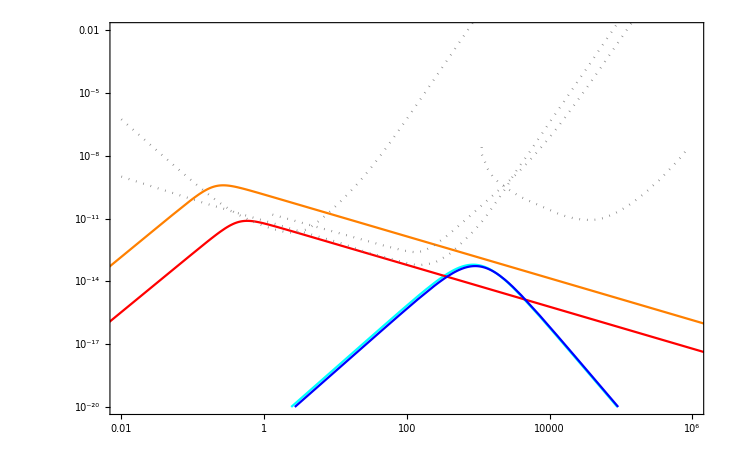

{(5.90577×10^-8 f^2.8)/(1+418.999 f^3.8),9.26219×10^-20 f^3 (1/(4+4.15318×10^-6 f^2))^(7/2),(1.3594×10^-10 f^2.8)/(1+22.1925 f^3.8),6.52503×10^-20 f^3 (1/(4+3.64226×10^-6 f^2))^(7/2)}

```mathematica
(*gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γϕ_,method_,verbose_:False,hh_:0.67,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwf_List:{Automatic,0,106.75,True,0},δxLargePrecAccu_List:{1/1000000,1000,30,20}]*)

IRs={Automatic,0,gSM,True,0};

Print["*****************"]
Print["No 0-modes:"]
Print["................."]
gwS=gwSpectra[{gDSUV,gVSUV},vwc,pars,Tcr,Hdec,Gam,"numeric",verbose,h,{1,False},{250,False,True},IRs,{10^-6,10^3,30,20}];
Print["*****************"]
Print["With 0-modes:"]
Print["................."]
gwS=gwS~Join~gwSpectra[{gDSUV,gVSUV},vwc,pars,Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^3,30,20}];

p1=LogLogPlot[gwS,{f,0.001,10^9},PlotStyle->{Orange,Cyan,Red,Blue},Frame->True,PlotRange->(*All*){{0.01,10^6},{10^-20,0.01}},PlotLegends->Placed[LineLegend[{MaTeX["\\text{Hot, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Hot, w/ 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/ 0-modes}",Magnification->1.2]}],{0.3,0.15}]];
p2=ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotStyle->{{Gray,Dotted}}];
Show[p1,p2]
(*Export[PlotsDir<>"sgwb.pdf",%]*)

gwS

Clear[gDSUV,gVSUV,gs,vwc,μ,A,λ,Δ,pars,Tcr,eff,gam,regime,Hdec,Gam,verbose,IRs,gwS,p1,p2,tofx,dlntdt,d2lntdt2,xC1,xMAX,xC2,Tmx,domain,Tpt,tpt,SE2Max,n0,n00m,Lmlnh1,Lmlnh2,Lmlnh3,LnbLx,xData,yData]
```

γ=0.02

```mathematica
gs100=(6.121138745726295*^-8 f^2.8)/(1+374.07046406940015 f^3.8);
Solve[D[gs100,f]==0,f,Reals]
pk100=gs100/.%⟦-1⟧

gs10=(5.903405859856274*^-8 f^2.8)/(1+163.00340985003146 f^3.8);
Solve[D[gs10,f]==0,f,Reals]
pk10=gs10/.%⟦-1⟧

pk10/pk100

Clear[gs100,pk100,gs10,pk10]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{f→0.},{f→0.},{f→0.275791}}

4.37193×10^-10

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{f→0.},{f→0.},{f→0.343175}}

7.77614×10^-10

1.77865

γ=50

```mathematica
gs100=(6.557588299874262*^-7 f^2.8)/(1+617.7544375761125 f^3.8);
Solve[D[gs100,f]==0,f,Reals]
pk100=gs100/.%⟦-1⟧

gs10=(8.167392650117525*^-6 f^2.8)/(1+123.65697149101396 f^3.8);
Solve[D[gs10,f]==0,f,Reals]
pk10=gs10/.%⟦-1⟧

pk10/pk100

Clear[gs100,pk100,gs10,pk10]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{f→0.},{f→0.},{f→0.241684}}

3.23634×10^-9

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{f→0.},{f→0.},{f→0.369053}}

1.31871×10^-7

40.747

```mathematica
{(6.557588299874262*^-7 f^2.8)/(1+617.7544375761125 f^3.8),7.238998379407702*^-23 f^3 (1/(4+3.5173707000667365*^-6 f^2))^(7/2),(1.541597036721476*^-8 f^2.8)/(1+14.982376931116502 f^3.8),6.78880389714839*^-23 f^3 (1/(4+3.572795851685521*^-6 f^2))^(7/2)}
```

#### Other

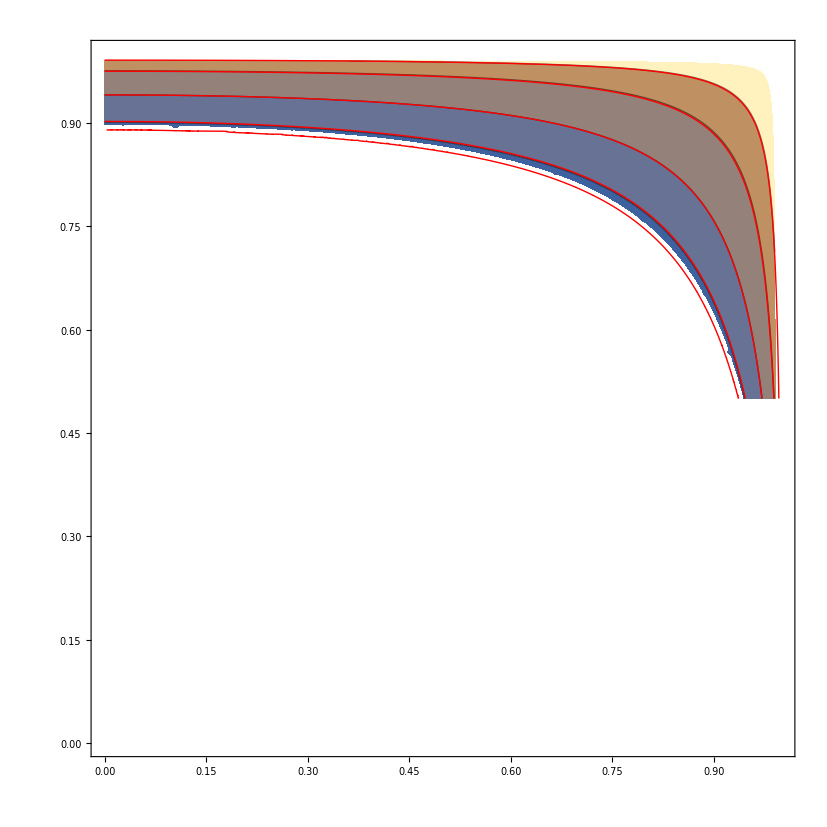

```mathematica
Aval=((A/.dePrivFn["PT",ARule])/.{μ->2,λ->1});
p1=ContourPlot[Log10[SETemp[{2,Aval,1},500,500/t]],{t,0,1},{Δ,0,1},Contours->Table[i,{i,1,5}],MaxRecursion->4];

log10SE=Log10[approxSE/.{μ->2,λ->1,θ->1/t}];
p2=ContourPlot[log10SE,{t,0,1},{Δ,0,1},Contours->Table[i,{i,1,5}],MaxRecursion->4,ContourStyle->Red,ContourShading->None];

Show[p1,p2]

Clear[Aval,log10SE]
```

-Graphics-

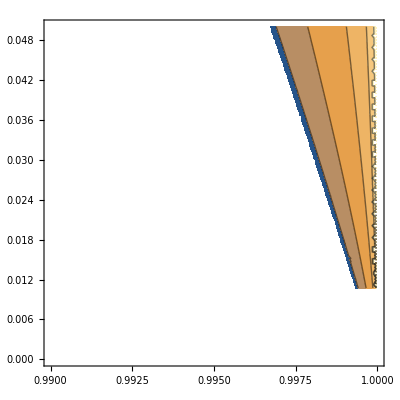

```mathematica
log10SE=Log10[approxSE/.{μ->2,λ->1,θ->1/t}];
p1=ContourPlot[log10SE,{t,0,1},{Δ,0,1},Contours->Table[i,{i,1,5}],MaxRecursion->4];

((((λbar/.dePrivFn["PT",newdefs])/.T->Tc/t)/.dePrivFn["PT",ARule])//Simplify);
p2=ContourPlot[%,{t,0,1},{Δ,0,1},Contours->{9/8},ContourStyle->{Red},ContourShading->None];

p3=ContourPlot[log10SE,{t,0,1},{Δ,0,1},Contours->{Log10[4Log[mpl/500]]},ContourStyle->{Darker@Green},ContourShading->None];
Show[p1,p2,p3]

ContourPlot[log10SE,{t,0.99,1},{Δ,0,0.05},Contours->Table[i,{i,1,5}]]

Clear[log10SE,p1,p2,p3]
```

```mathematica
(*gwSpectra[gStar_,vwCool_,coeffs_List,Tcrit_,Hd_,Γϕ_,method_,instantVSRH_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxScaleFac_List:{250,False},wfgdIRxiIRTIR_List:{0,0,0,10^3},δxLargePrecAccu_List:{10^-6,10^3,30,20}]*)
```

{μ,A,λ}={0.6,0.284605,1}

T_c exists: True

T_s=513.956

f=3.76669

{x_c1,x_max,x_c2}={0.667,0.721,7.266}

T_max=1764.78 GeV

x_PT=0.667

T_PT=509.057 GeV

λ̄(T_max)=3.14604 (should be smaller than 9/8=1.125)

log_10(Γ/𝒱)_T_max=(29.9031+(0.996108-3.35254 ⅈ) Null)/Log[10]

S_E(T_max)=(-0.996108+3.35254 ⅈ) Null

S_E(T_max)/(4×ln[m_Pl/T_c])=(-0.00689405+0.0232029 ⅈ) Null

S_E''(T_max)=(7.87782×10^-23-1.47461×10^-22 ⅈ) Null

For supracritical 1PT:

w/o 0-modes: n_0 = (2.4314×10^13 ⅇ^((0.996108-3.35254 ⅈ) Null))/(√((7.87782×10^-23-1.47461×10^-22 ⅈ) Null)),  (8π·n_0·v_w^3)^(1/3) = 84859.2 (ⅇ^((0.996108-3.35254 ⅈ) Null)/(√((7.87782×10^-23-1.47461×10^-22 ⅈ) Null)))^(1/3)

w/ 0-modes: n_0 = (2.4314×10^13 ⅇ^((0.996108-3.35254 ⅈ) Null) ((-0.158536+0.533574 ⅈ) Null)^(3/2))/(√((7.87782×10^-23-1.47461×10^-22 ⅈ) Null)),  (8π·n_0·v_w^3)^(1/3) = 84859.2 ((ⅇ^((0.996108-3.35254 ⅈ) Null) ((-0.158536+0.533574 ⅈ) Null)^(3/2))/(√((7.87782×10^-23-1.47461×10^-22 ⅈ) Null)))^(1/3)

w/ 0-modes: n_b = 2.66709×10^-15,  β_eff = 0.0000406218

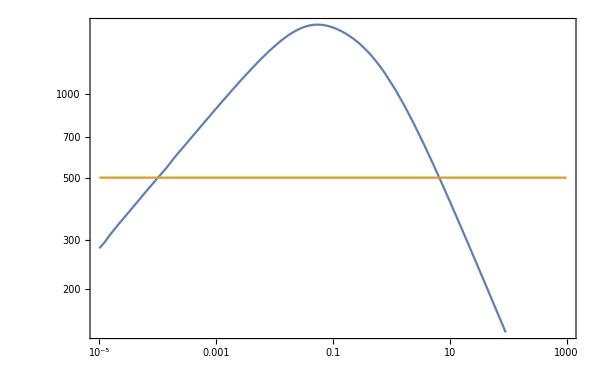

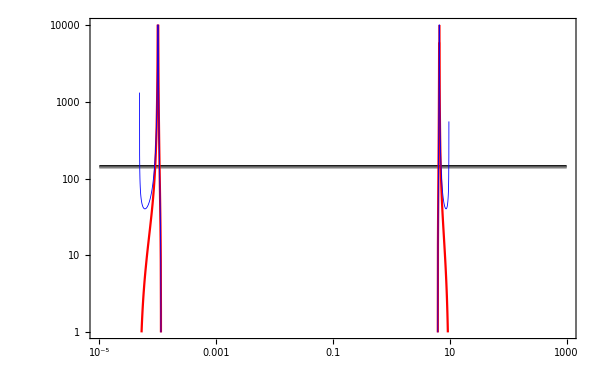

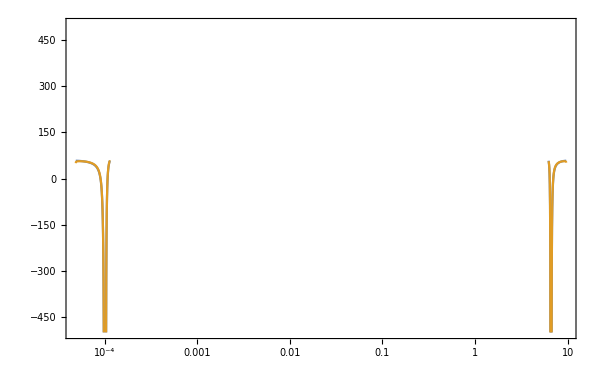

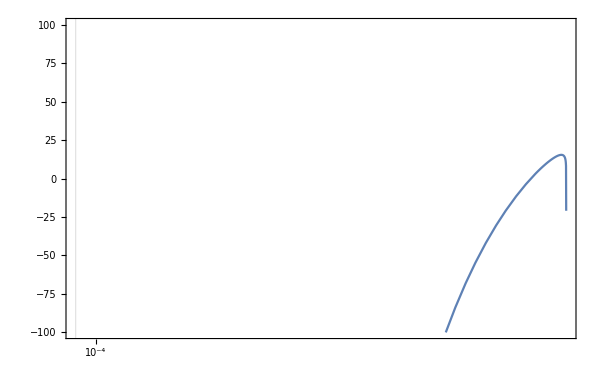

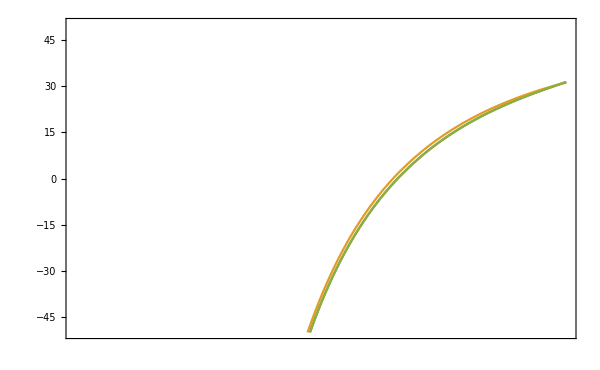

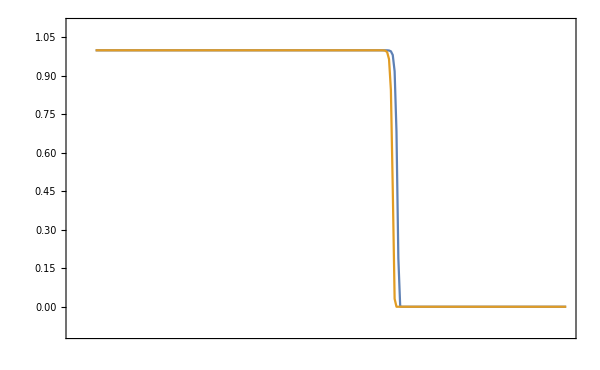

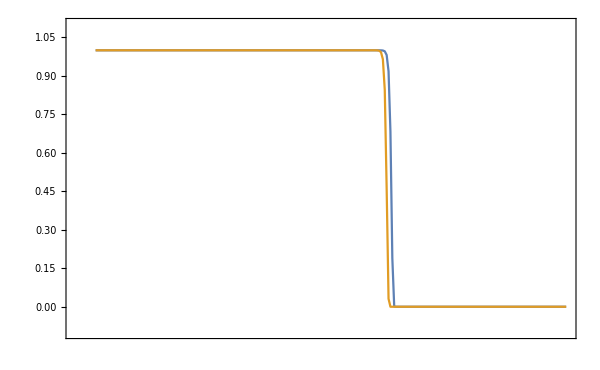

*****************

No 0-modes:

.................

t_max=4.728*10^11
x_max=7.212*10^-1
T_max=1.765*10^3
t_c={4.372*10^11, 4.764*10^12}
x_c={6.668*10^-1, 7.266}
T_PT={5.092*10^2, 4.845*10^2}
t_PT={4.372*10^11, 5.065*10^12}
x_PT={6.668*10^-1, 7.726}
λ̄={1.083, 8.487*10^-1}
χ_b={5.183*10^2, 6.187*10^2}
ϵ={3.56*10^8, 6.624*10^8}
E_c={3.472*10^4, 5.051*10^4}
S_E={6.818*10^1, 1.042*10^2}
S_E'={-4.411*10^-5, -5.509*10^-10}
S_E''={2.674*10^-11, 4.887*10^-21}
Γ/V={1.641*10^-19, 2.964*10^-35}
β_1={4.412*10^-5, 5.505*10^-10}
β_2={-2.674*10^-11, -4.887*10^-21}
n_b={2.435*10^-15, 2.838*10^-26}
R_b={7.433*10^4, 3.279*10^8}
⟨R⟩={2.926*10^4, 1.748*10^8}
β_eff={3.941*10^-5, 4.467*10^-10}
α_∞={-5.669*10^-2, 8.921*10^-2}
α_n={1.61*10^-3, 3.653*10^-3}
κ_eff={3.622*10^1, -2.342*10^1}
H_*={1.525*10^-12, 1.01*10^-13}
R={5.447*10^-3, 1.004}
Z={1.31*10^16, 3.355*10^15}

*****************

With 0-modes:

.................

t_max=4.728*10^11
x_max=7.212*10^-1
T_max=1.765*10^3
t_c={4.372*10^11, 4.764*10^12}
x_c={6.668*10^-1, 7.266}
T_PT={5.091*10^2, 4.849*10^2}
t_PT={4.372*10^11, 5.058*10^12}
x_PT={6.668*10^-1, 7.715}
λ̄={1.082, 8.523*10^-1}
χ_b={5.193*10^2, 6.178*10^2}
ϵ={3.513*10^8, 6.467*10^8}
E_c={3.647*10^4, 5.253*10^4}
S_E={7.165*10^1, 1.083*10^2}
S_E'={-4.624*10^-5, -5.877*10^-10}
S_E''={2.849*10^-11, 5.365*10^-21}
Γ/V={1.975*10^-19, 3.524*10^-35}
β_1={4.529*10^-5, 5.792*10^-10}
β_2={-2.852*10^-11, -5.334*10^-21}
n_b={2.667*10^-15, 3.062*10^-26}
R_b={7.211*10^4, 3.196*10^8}
⟨R⟩={2.855*10^4, 1.729*10^8}
β_eff={4.062*10^-5, 4.582*10^-10}
α_∞={-5.694*10^-2, 8.883*10^-2}
α_n={1.59*10^-3, 3.556*10^-3}
κ_eff={3.681*10^1, -2.398*10^1}
H_*={1.525*10^-12, 1.011*10^-13}
R={5.441*10^-3, 1.004}
Z={1.31*10^16, 3.357*10^15}

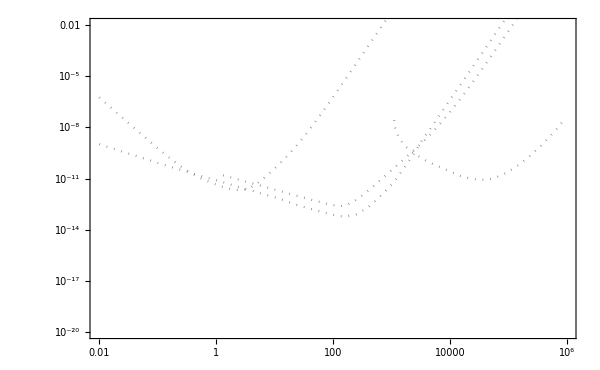

{(2.37001×10^-44 f^2.8)/(1+3.69534×10^-23 f^3.8),2.19036×10^-30 f^3 (1/(4+1.37432×10^-7 f^2))^(7/2),(2.06065×10^-44 f^2.8)/(1+3.29294×10^-23 f^3.8),1.78351×10^-30 f^3 (1/(4+1.30809×10^-7 f^2))^(7/2)}

```mathematica
verbose=True;
gs=10;
vwc=0.05;

(*
(*VERY STRONG 1PT: Subscript[α, n]>1 ⇒ vacuum energy is important ⇒ evolution during RH is suspect*)
μ=10;
λ=3;*)
μ=0.6;
λ=1;
(*Δ=8/9+0.02;*)
(*Δ=8/9-0.0001;*)
Δ=0.3;
A=(A/.(dePrivFn["PT",ARule]));
pars={μ,A,λ};
Print["{μ,A,λ}=",pars]
Print["T_c exists: ",dePrivFn["PT",cond1,pars⟦1⟧,pars⟦2⟧,pars⟦3⟧]]

Tcr=500GeV;

Print["T_s=",(Ts/.dePrivFn["PT",Tspinodal])/.Tc->Tcr]

gam=50;
regime=If[gam≤1,"γ<<1","γ>>1"];
(*Print["f∈[",((dePrivFn["RH",RHDict["fmin"][regime]])/.γ->gam)//N,", ",(fMax[regime]/.γ->gam)//N,"]"]*)

eff=If[regime=="γ<<1",1.03*(1.7/gam^(1/4)),3.3*(1+1./gam^(1/2))];
Print["f=",eff]

solEqs[gam];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);Gam=gam*Hdec;

tofx=TOfx[Gam/Hdec,gs,Hdec];
dlntdt[x_]=Hdec*D[tofx[x],x]/tofx[x];
d2lntdt2[x_]=Hdec*D[dlntdt[x],x];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];
SE2Max=S2Rate[dlntdt[xMAX],d2lntdt2[xMAX],pars,Tcr,Tmx];

{Tpt,tpt,λbarr,Xbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{tofx,1/Hdec},pars,Tcr,"numeric",1,True,{1,1},250];

GV=(Γnucl[pars,Tcr,tofx[xMAX],1,False]);
GV0m=(Γnucl[pars,Tcr,tofx[xMAX],1,True]);
n0=(√(2π))/(√SE2Max)GV;
n00m=(√(2π))/(√SE2Max)GV0m;

Print["{x_c1,x_max,x_c2}=",Round[#,0.001]&/@{xC1,xMAX,xC2}]
Print["T_max=",Tmx," GeV"]
Print["x_PT=",Round[tpt*Hdec,0.001]]
Print["T_PT=",Tpt," GeV"]
Print["λ̄(T_max)=",(dePrivFn["PT",λbar]/.dePrivFn["PT",McλbarToCoeffs])/.{Tc->Tcr,T->Tmx}," (should be smaller than 9/8=1.125)"]
Print["log_10(Γ/𝒱)_T_max=",Γnucl[pars,Tcr,Tmx,1,False,True]]
Print["S_E(T_max)=",SETemp[pars,Tcr,Tmx]]
Print["S_E(T_max)/(4×ln[m_Pl/T_c])=",SETemp[pars,Tcr,Tmx]/(4Log[mpl/Tcr])]
Print["S_E''(T_max)=",SE2Max]
Print["For supracritical 1PT:"]
Print["w/o 0-modes: n_0 = ",n0,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n0 1^3)^(1/3)]
Print["w/ 0-modes: n_0 = ",n00m,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n00m 1^3)^(1/3)]
Print["w/ 0-modes: n_b = ",nbub,",  β_eff = ",beff]

Clear[λbarr,Xbb,epss,Ecr,SEu,SE1,SE2,GV,GV0m,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff]


LogLogPlot[{tofx[2/3+dx],Tcr},{dx,10^-5,domain⟦-1⟧-2/3},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\mathrm{Temperature}\\ [\\mathrm{GeV}]",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["T_\\mathrm{rh}(x)",Magnification->1.7],MaTeX["T_\\mathrm{c}",Magnification->1.7]}],{0.9,0.85}]]

LogLogPlot[{4Log[mpl/Tcr],4Log[mpl/Tmx],SETemp[pars,Tcr,tofx[2/3+dx]],approxSE/.{θ->(tofx[2/3+dx]/Tcr)},SETemp[pars,Tcr,tofx[xMAX]]+SE2Max*1/2((2/3+dx)-xMAX)^2*Hdec^-2},{dx,10^-5,domain⟦-1⟧-2/3},Frame->True,PlotRange->{1,10^4},PlotStyle->{Black,Gray,Red,{Blue,Thickness[0.001]},Darker@Green},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["S_\\mathrm{E}",Magnification->2]},PlotLabel->MaTeX["\\text{Euclidean Action}",Magnification->1.7],PlotLegends->Placed[LineLegend[{MaTeX["4 \\ln(m_\\mathrm{Pl}/T_\\mathrm{c})",Magnification->1],MaTeX["4 \\ln(m_\\mathrm{Pl}/T_\\mathrm{max})",Magnification->1],MaTeX["S_E(x)",Magnification->1],MaTeX["S_E^\\mathrm{ appx.}(x)",Magnification->1],MaTeX["S_E^{\\prime\\prime}(t-t_\\mathrm{max})^2 /2",Magnification->1]}],{0.2,0.25}]]
(*Export[PlotsDir<>"SE_x.pdf",%]*)

LogLinearPlot[{Γnucl[pars,Tcr,tofx[2/3+dx],1,False,True]-4Log10[Hdec],Γnucl[pars,Tcr,tofx[2/3+dx],1,True,True]-4Log10[Hdec]},{dx,10^-5,domain⟦-1⟧-2/3},Frame->True,PlotRange->{-500,500},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H_\\mathrm{dec}^4)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.7],MaTeX["\\text{w/ 0-modes}",Magnification->1.7]}],{0.8,0.85}]]

LogLinearPlot[{Log[4/3 π*1^3(2/3+dx)((tpt*Hdec)-(2/3+dx))^3]+Γnucl[pars,1,tofx[2/3+dx]/Tcr,1,True,True]*Log[10]+4Log[Tcr/Hdec]},{dx,xC1-2/3,(tpt*Hdec)-2/3},Frame->True,PlotRange->{-100,100},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[J(x_{\\rm PT},x')]",Magnification->2]},PlotLabel->MaTeX["\\text{Origin of Bubbles}",Magnification->1.7],GridLines->{{(xC1-2/3)}~Join~{xMAX - 2/3},None}]
(*Export[PlotsDir<>"I_x.pdf",%]*)

(*h(x) w/o scale factor*)
Lmlnh1=Lmlnh["hot",1,{tofx,1/Hdec},pars,Tcr,1,False,{1,1},250];

(*Subscript[n, b](x) w/o scale factor*)
LnbLx=Lnbubble[Lmlnh1,{tofx,1/Hdec},pars,Tcr,1,False,{1,1}];
xData=(InterpolatingFunctionCoordinates[LnbLx]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[LnbLx]//Flatten);
LnbLx={(10^xData)-2/3,10^yData}//Transpose;

xData=(InterpolatingFunctionCoordinates[Lmlnh1]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh1]//Flatten);
Lmlnh1={(10^xData)-2/3,yData}//Transpose;

Lmlnh2=Lmlnh["hot",1,{tofx,1/Hdec},pars,Tcr,1,True,{1,1},250];

xData=(InterpolatingFunctionCoordinates[Lmlnh2]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh2]//Flatten);
Lmlnh2={(10^xData)-2/3,yData}//Transpose;

Lmlnh3=Lmlnh["hot",1,{tofx,1/Hdec},pars,Tcr,1,False,{1,1},500];
xData=(InterpolatingFunctionCoordinates[Lmlnh3]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh3]//Flatten);
Lmlnh3={(10^xData)-2/3,yData}//Transpose;

ListLogLinearPlot[{Lmlnh1,Lmlnh2,Lmlnh3},Joined->True,PlotRange->{-50,50},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10} (-\\ln h(x))",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2],MaTeX["\\text{w/o 0-modes; more steps}",Magnification->1.2]}],{0.3,0.75}]]

Lmlnh1=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh2);

ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.2,0.15}],GridLines->{{xMAX - 2/3}~Join~{tpt*Hdec - 2/3},{1/E}}]

Lmlnh1=({#⟦1⟧+2/3,#⟦2⟧}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧+2/3,#⟦2⟧}&/@Lmlnh2);

p1=ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["t H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.8,0.85}],GridLines->{{xMAX }~Join~{tpt*Hdec},{1/E}}];
p2=LogLinearPlot[{Exp[-(4π)/3*(n0/Hdec^3)*1^3*(x-xMAX)^3],Exp[-(4π)/3*(n00m/Hdec^3)*1^3*(x-xMAX)^3]},{x,Lmlnh1⟦1,1⟧,Lmlnh1⟦-1,1⟧},PlotStyle->{Darker@Green,Red},PlotRange->{-0.1,1.1},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes; analytic, simultaneous}",Magnification->1.2],MaTeX["\\text{w 0-modes; analytic, simultaneous}",Magnification->1.2]}],{0.7,0.65}]];
Show[p1,p2]

(*p1=ListLogLogPlot[LnbLx,Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["t H_i",Magnification->2],MaTeX["n_b",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["n_b",Magnification->1.7]}],{0.9,0.85}],GridLines->{{xMAX }~Join~{tpt*Hdec},{1/E}}];*)

(*gwSpectra[gStar_,vwCool_,coeffs_List,Tcrit_,Hd_,Γϕ_,method_,instantVSRH_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxScaleFac_List:{250,False},wfgdIRxiIRTIR_List:{0,0,0,10^3},δxLargePrecAccu_List:{10^-6,10^3,30,20}]*)

Print["*****************"]
Print["No 0-modes:"]
Print["................."]
gwS=gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"numeric",True,verbose,h,{1,False},{250,False,True}];
Print["*****************"]
Print["With 0-modes:"]
Print["................."]
gwS=gwS~Join~gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"numeric",True,verbose,h,{1,True},{250,False,True}];

p1=LogLogPlot[gwS,{f,0.001,10^9},PlotStyle->{Orange,Cyan,Red,Blue},Frame->True,PlotRange->(*All*){{0.01,10^6},{10^-20,0.01}},PlotLegends->Placed[LineLegend[{MaTeX["\\text{Hot, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Hot, w/ 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/ 0-modes}",Magnification->1.2]}],{0.3,0.15}]];
p2=ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotStyle->{{Gray,Dotted}}];
Show[p1,p2]
(*Export[PlotsDir<>"sgwb.pdf",%]*)

gwS

Clear[gs,vwc,μ,A,λ,Δ,pars,Tcr,eff,gam,regime,Hdec,Gam,verbose,gwS,p1,p2,tofx,dlntdt,d2lntdt2,xC1,xMAX,xC2,Tmx,domain,Tpt,tpt,SE2Max,n0,n00m,Lmlnh1,Lmlnh2,Lmlnh3,LnbLx,xData,yData]
```

{μ,A,λ}={1,0.825631,1}

T_c exists: True

T_s=0.-1006.15 ⅈ

f=3.76669

{x_c1,x_max,x_c2}={0.667,0.721,7.266}

T_max=1764.78 GeV

x_PT=0.776

T_PT=1711.25 GeV

λ̄(T_max)=1.0922 (should be smaller than 9/8=1.125)

log_10(Γ/𝒱)_T_max=-44.6241

S_E(T_max)=132.654

S_E(T_max)/(4×ln[m_Pl/T_c])=0.918096

S_E''(T_max)=1.08762×10^-20

For supracritical 1PT:

w/o 0-modes: n_0 = 5.71119×10^-35,  (8π·n_0·v_w^3)^(1/3) = 1.12803×10^-11

w/ 0-modes: n_0 = 5.54035×10^-33,  (8π·n_0·v_w^3)^(1/3) = 5.18313×10^-11

w/ 0-modes: n_b = 5.36041×10^-33,  β_eff = 5.1264×10^-11

*****************

w/o scale factor:

.................

t_max=4.728*10^11
x_max=7.212*10^-1
T_max=1.765*10^3
t_c={4.372*10^11, 4.764*10^12}
x_c={6.668*10^-1, 7.266}
T_PT={1.711*10^3, 2.605*10^2}
t_PT={5.087*10^11, 1.725*10^13}
x_PT={7.759*10^-1, 2.631*10^1}
λ̄={1.092, 7.309*10^-1}
χ_b={4.968*10^3, 1.027*10^3}
ϵ={3.492*10^12, 7.53*10^9}
E_c={2.325*10^5, 3.134*10^4}
S_E={1.359*10^2, 1.203*10^2}
S_E'={1.283*10^-10, -1.604*10^-11}
S_E''={7.728*10^-22, 3.127*10^-24}
Γ/V={8.356*10^-45, 2.177*10^-41}
β_1={-1.315*10^-10, 1.572*10^-11}
β_2={-7.794*10^-22, -3.108*10^-24}
n_b={5.36*10^-33, 7.447*10^-31}
R_b={5.714*10^10, 1.103*10^10}
⟨R⟩={3.291*10^10, 4.541*10^9}
β_eff={5.126*10^-11, 1.328*10^-11}
α_∞={-1.281, 2.363}
α_n={1.238*10^-1, 4.972*10^-1}
κ_eff={1.135*10^1, -3.753}
H_*={1.262*10^-12, 2.918*10^-14}
R={1.119, 1.497}
Z={1.186*10^16, 1.803*10^15}

*****************

w/ scale factor:

.................

t_max=4.728*10^11
x_max=7.212*10^-1
T_max=1.765*10^3
t_c={4.372*10^11, 4.764*10^12}
x_c={6.668*10^-1, 7.266}
T_PT={1.709*10^3, 2.605*10^2}
t_PT={5.098*10^11, 1.725*10^13}
x_PT={7.775*10^-1, 2.631*10^1}
λ̄={1.092, 7.309*10^-1}
χ_b={4.962*10^3, 1.027*10^3}
ϵ={3.474*10^12, 7.53*10^9}
E_c={2.325*10^5, 3.133*10^4}
S_E={1.36*10^2, 1.203*10^2}
S_E'={1.29*10^-10, -1.603*10^-11}
S_E''={7.253*10^-22, 3.126*10^-24}
Γ/V={7.309*10^-45, 2.199*10^-41}
β_1={-1.323*10^-10, 1.572*10^-11}
β_2={-7.306*10^-22, -3.107*10^-24}
n_b={4.704*10^-33, 7.462*10^-31}
R_b={5.968*10^10, 1.103*10^10}
⟨R⟩={3.43*10^10, 4.532*10^9}
β_eff={4.908*10^-11, 1.328*10^-11}
α_∞={-1.281, 2.363}
α_n={1.237*10^-1, 4.972*10^-1}
κ_eff={1.135*10^1, -3.752}
H_*={1.259*10^-12, 2.917*10^-14}
R={1.119, 1.497}
Z={1.185*10^16, 1.803*10^15}

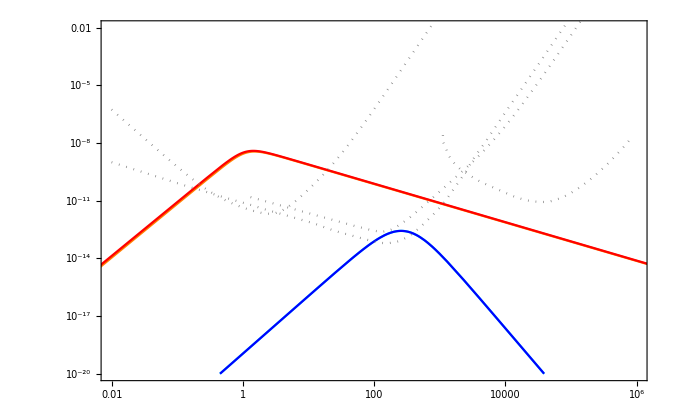

{(4.3505×10^-9 f^2.8)/(1+0.588152 f^3.8),1.41907×10^-17 f^3 (1/(4+0.0000449735 f^2))^(7/2),(5.31948×10^-9 f^2.8)/(1+0.690598 f^3.8),1.41543×10^-17 f^3 (1/(4+0.0000449135 f^2))^(7/2)}

.................

```mathematica
verbose=True;
gs=10;
vwc=0.05;

(*
(*VERY STRONG 1PT: Subscript[α, n]>1 ⇒ vacuum energy is important ⇒ evolution during RH is suspect*)
μ=10;
λ=3;*)
μ=1;
λ=1;
Δ=8/9+0.02;
(*Δ=8/9-0.0001;*)
(*Δ=0.5;*)
A=(A/.(dePrivFn["PT",ARule]));
pars={μ,A,λ};
Print["{μ,A,λ}=",pars]
Print["T_c exists: ",dePrivFn["PT",cond1,pars⟦1⟧,pars⟦2⟧,pars⟦3⟧]]

Tcr=500GeV;

Print["T_s=",(Ts/.dePrivFn["PT",Tspinodal])/.Tc->Tcr]

gam=50;
regime=If[gam≤1,"γ<<1","γ>>1"];
(*Print["f∈[",((dePrivFn["RH",RHDict["fmin"][regime]])/.γ->gam)//N,", ",(fMax[regime]/.γ->gam)//N,"]"]*)

eff=If[regime=="γ<<1",1.03*(1.7/gam^(1/4)),3.3*(1+1./gam^(1/2))];
Print["f=",eff]

solEqs[gam];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);Gam=gam*Hdec;

tofx=TOfx[Gam/Hdec,gs,Hdec];
dlntdt[x_]=Hdec*D[tofx[x],x]/tofx[x];
d2lntdt2[x_]=Hdec*D[dlntdt[x],x];

domain=InterpolatingFunctionDomain[tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=tofx[xMAX];
SE2Max=S2Rate[dlntdt[xMAX],d2lntdt2[xMAX],pars,Tcr,Tmx];

{Tpt,tpt,λbarr,Xbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{tofx,1/Hdec},pars,Tcr,"numeric",1,True,{1,1},250];

GV=(Γnucl[pars,Tcr,tofx[xMAX],1,False]);
GV0m=(Γnucl[pars,Tcr,tofx[xMAX],1,True]);
n0=(√(2π))/(√SE2Max)GV;
n00m=(√(2π))/(√SE2Max)GV0m;

Print["{x_c1,x_max,x_c2}=",Round[#,0.001]&/@{xC1,xMAX,xC2}]
Print["T_max=",Tmx," GeV"]
Print["x_PT=",Round[tpt*Hdec,0.001]]
Print["T_PT=",Tpt," GeV"]
Print["λ̄(T_max)=",(dePrivFn["PT",λbar]/.dePrivFn["PT",McλbarToCoeffs])/.{Tc->Tcr,T->Tmx}," (should be smaller than 9/8=1.125)"]
Print["log_10(Γ/𝒱)_T_max=",Γnucl[pars,Tcr,Tmx,1,False,True]]
Print["S_E(T_max)=",SETemp[pars,Tcr,Tmx]]
Print["S_E(T_max)/(4×ln[m_Pl/T_c])=",SETemp[pars,Tcr,Tmx]/(4Log[mpl/Tcr])]
Print["S_E''(T_max)=",SE2Max]
Print["For supracritical 1PT:"]
Print["w/o 0-modes: n_0 = ",n0,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n0 1^3)^(1/3)]
Print["w/ 0-modes: n_0 = ",n00m,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n00m 1^3)^(1/3)]
Print["w/ 0-modes: n_b = ",nbub,",  β_eff = ",beff]

Clear[λbarr,Xbb,epss,Ecr,SEu,SE1,SE2,GV,GV0m,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff]

(*gwSpectra[gStar_,vwCool_,coeffs_List,Tcrit_,Hd_,Γϕ_,method_,instantVSRH_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxScaleFac_List:{250,False},wfgdIRxiIRTIR_List:{0,0,0,10^3},δxLargePrecAccu_List:{10^-6,10^3,30,20}]*)

Print["*****************"]
Print["w/o scale factor:"]
Print["................."]
gwS=gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"numeric",True,verbose,h,{1,True},{250,False,True}];
Print["*****************"]
Print["w/ scale factor:"]
Print["................."]
gwS=gwS~Join~gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"numeric",True,verbose,h,{1,True},{250,True,True}];

p1=LogLogPlot[gwS,{f,0.001,10^9},PlotStyle->{Orange,Cyan,Red,Blue},Frame->True,PlotRange->(*All*){{0.01,10^6},{10^-20,0.01}},PlotLegends->Placed[LineLegend[{MaTeX["\\text{Hot, w/o scale factor}",Magnification->1.2],MaTeX["\\text{Cold, w/o scale factor}",Magnification->1.2],MaTeX["\\text{Hot, w/ scale factor}",Magnification->1.2],MaTeX["\\text{Cold, w/ scale factor}",Magnification->1.2]}],{0.3,0.15}]];
p2=ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotStyle->{{Gray,Dotted}}];
Show[p1,p2]
(*Export[PlotsDir<>"sgwb.pdf",%]*)

gwS

Clear[gs,vwc,μ,A,λ,Δ,pars,Tcr,eff,gam,regime,Hdec,Gam,verbose,gwS,p1,p2,tofx,dlntdt,d2lntdt2,xC1,xMAX,xC2,Tmx,domain,Tpt,tpt,SE2Max,n0,n00m,Lmlnh1,Lmlnh2,Lmlnh3,LnbLx,xData,yData]
```

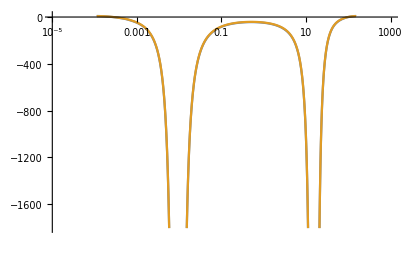

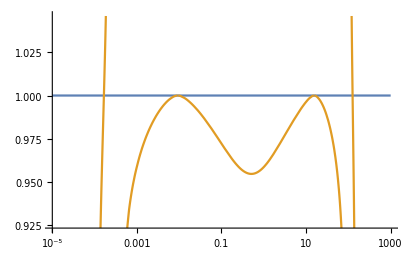

t_max=3.27*10^11
T_max=9.86*10^2
t_c={1.88*10^11, 4.5*10^12}
T_PT={9.82*10^2, 2.81*10^2}
t_PT={3.67*10^11, 1.56*10^13}
λ̄={1.09, 7.29*10^-1}
χ_b={1.99*10^3, 7.75*10^2}
ϵ={4.56*10^10, 1.23*10^9}
E_c={1.26*10^5, 3.3*10^4}
Γ/V={1.04*10^-44, 5.53*10^-42}
β={-7.54*10^-11, 1.88*10^-11}
α_∞={-1.56*10^-1, 2.89*10^-1}
α_n={1.49*10^-2, 5.99*10^-2}
κ_eff={1.15*10^1, -3.83}
H_*={1.81*10^-12, 3.41*10^-14}
R={5.34*10^-2, 1.05}
Z={1.94*10^16, 1.95*10^15}

t_max=3.27*10^11
T_max=9.86*10^2
t_c={1.88*10^11, 4.5*10^12}
T_PT={9.85*10^2, 2.81*10^2}
t_PT={3.16*10^11, 1.56*10^13}
λ̄={1.09, 7.29*10^-1}
χ_b={2.*10^3, 7.75*10^2}
ϵ={4.64*10^10, 1.23*10^9}
E_c={1.25*10^5, 3.31*10^4}
Γ/V={4.72*10^-44, 4.94*10^-42}
β={3.3*10^-11, 1.88*10^-11}
α_∞={-1.56*10^-1, 2.89*10^-1}
α_n={1.5*10^-2, 5.99*10^-2}
κ_eff={1.14*10^1, -3.83}
H_*={2.1*10^-12, 3.41*10^-14}
R={4.01*10^-2, 1.05}
Z={2.14*10^16, 1.95*10^15}

t_max=3.27*10^11
T_max=9.86*10^2
t_c={1.88*10^11, 4.5*10^12}
T_PT={1.03*10^3, 2.82*10^2}
t_PT={2.36*10^11, 2.01*10^13}
λ̄={1.1, 7.32*10^-1}
χ_b={2.07*10^3, 7.77*10^2}
ϵ={5.64*10^10, 1.23*10^9}
E_c={1.15*10^5, 3.38*10^4}
Γ/V={2.35*10^-37, 5.51*10^-43}
β={1.56*10^-9, 1.08*10^-11}
α_∞={-1.54*10^-1, 2.89*10^-1}
α_n={1.53*10^-2, 5.91*10^-2}
κ_eff={1.1*10^1, -3.88}
H_*={2.82*10^-12, 2.61*10^-14}
R={1.7*10^-2, 1.06}
Z={2.6*10^16, 1.71*10^15}

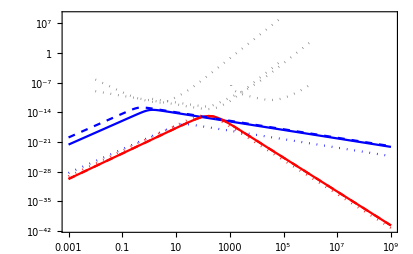

{(6.5567×10^-14 f^2.8)/(1+0.878785 f^3.8),2.64655×10^-19 f^3 (1/(4+0.000105512 f^2))^(7/2),(3.166×10^-12 f^2.8)/(1+29.6298 f^3.8),2.62854×10^-19 f^3 (1/(4+0.000105282 f^2))^(7/2),(1.32463×10^-20 f^2.8)/(1+0.0000269203 f^3.8),1.16853×10^-18 f^3 (1/(4+0.000241233 f^2))^(7/2)}

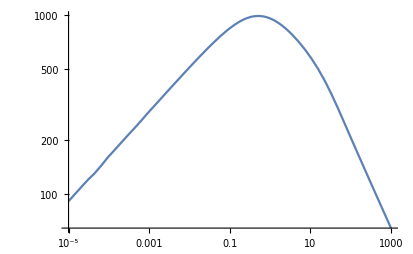

```mathematica
verbose=True;
gs=10;
vwc=0.1;

μ=0.5;
λ=0.5;
A=(√(2/3) √λ μ)(1-10^-5);
pars={μ,A,λ};
(*pars={1.,0.8,1.};*)

Tcr=500GeV;

Hdec=35*Tcr^2/mpl;Gam=Hdec/10;

tofx=TOfx[Gam/Hdec,gs,Hdec];
domain=InterpolatingFunctionDomain[tofx]//Flatten;

LogLinearPlot[{ptParams`Private`Γnucl[pars,Tcr,tofx[2/3+dx],1,False,True],ptParams`Private`Γnucl[pars,Tcr,tofx[2/3+dx],1,True,True]},{dx,10^-5,domain⟦-1⟧-2/3}]

LogLinearPlot[{1.,ptParams`Private`Γnucl[pars,Tcr,tofx[2/3+dx],1,True,True]/ptParams`Private`Γnucl[pars,Tcr,tofx[2/3+dx],1,False,True]},{dx,10^-5,domain⟦-1⟧-2/3}]

gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"numeric",True,verbose];
gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"semi",True,verbose];
gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"analytic",True,verbose];
gwS=%%%~Join~%%~Join~%;

p1=LogLogPlot[gwS,{f,0.001,10^9},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed},{Blue,Dotted},{Red,Dotted}},Frame->True,PlotRange->All];
p2=ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotStyle->{{Gray,Dotted}}];
Show[p1,p2]

gwS

LogLogPlot[tofx[2/3+dx],{dx,10^-5,domain⟦-1⟧-2/3}]

Clear[gs,vwc,μ,A,λ,pars,Tcr,Hdec,Gam,verbose,gwS,p1,p2,tofx,dtofx,domain]
```

1-(4 A^2)/(3 λ μ^2)

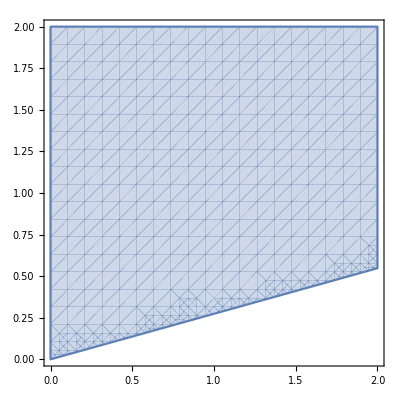
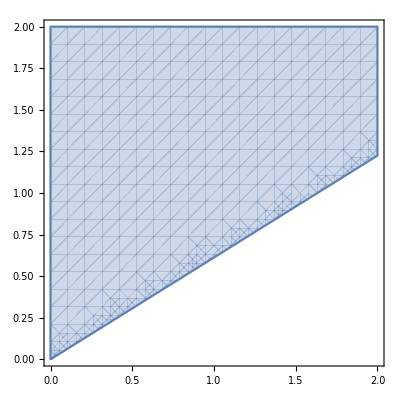
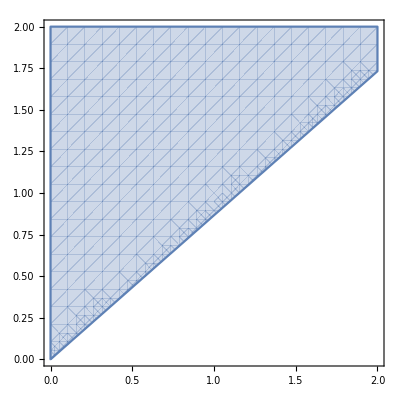
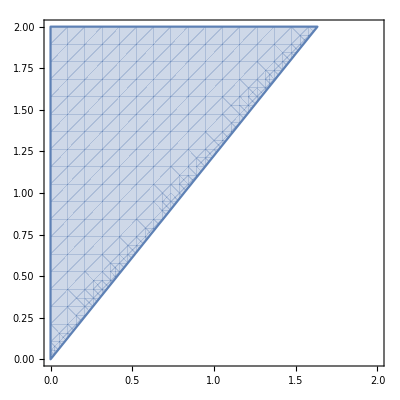
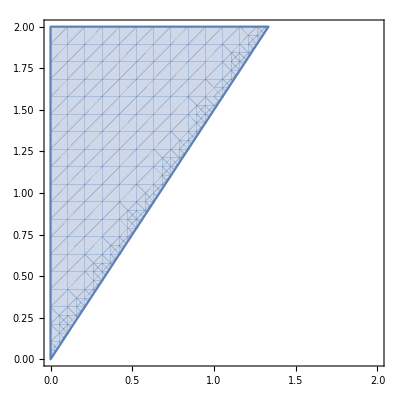

```mathematica
1-4/3 A^2/(λ μ^2)
Table[RegionPlot[(%)<0,{μ,0,2},{A,0,2}],{λ,{0.1,0.5,1,2,3}}]
```

t_max=5.82*10^10
T_max=1.58*10^3
t_c={3.36*10^10, 5.38*10^11}
T_PT={1.38*10^3, 6.95*10^2}
t_PT={3.81*10^10, 1.88*10^12}
λ̄={1.08, 8.16*10^-1}
χ_b={1.98*10^3, 1.27*10^3}
ϵ={7.42*10^10, 1.36*10^10}
E_c={1.42*10^5, 7.45*10^4}
Γ/V={1.23*10^-32, 6.33*10^-36}
β={2.36*10^-8, 1.12*10^-10}
α_∞={-7.82*10^-2, 1.27*10^-1}
α_n={6.18*10^-3, 1.78*10^-2}
κ_eff={1.37*10^1, -6.16}
H_*={1.75*10^-11, 3.32*10^-13}
R={2.22*10^-3, 3.98*10^-1}
Z={8.46*10^16, 6.57*10^15}

{(4.47959×10^-26 f^2.8)/(1+7.84337×10^-8 f^3.8),2.7848×10^-29 f^3 (1/(4+3.33723×10^-7 f^2))^(7/2)}

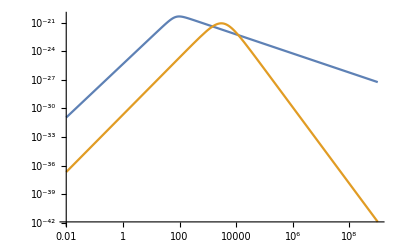

```mathematica
gwSpectra[10,0.01,{0.5,0.4,1},1000GeV,50*(1000GeV)^2/mpl,1*(1000GeV)^2/mpl,"numeric",True,True]
LogLogPlot[%,{f,0.01,10^9}]
```

```mathematica
gs=10;
vwc=0.1;
(*pars={0.5,0.8*0.5,1};*)
pars={0.8,0.61,1};
Tcr=500GeV;
Hdec=20*Tcr^2/mpl;
Gam=Hdec/25;


gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"numeric",True,True]

{Ωboil,Ωcool}=gwSpectra[gs,vwc,pars,Tcr,Hdec,Gam,"numeric",True,False];
Print[{Ωboil,Ωcool}]

Show[LogLogPlot[{Ωboil,
Ωcool},{f,10^-3,10^8},PlotRange->{{10^-2,10^6},{10^-14,10^-10}},Frame->True,ImageSize->800,FrameTicks->{{fticksR2[10^-100,10^10,2],fticksRNoLabels[10^-100,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["f~[\\textrm{mHz}]",Magnification->2],MaTeX["\\Omega_\\textrm{GW}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\Omega_\\textrm{env, \\textrm{boiling}}",Magnification->1.5],MaTeX["\\Omega_\\textrm{sw, \\textrm{cooling}}",Magnification->1.5]}],{0.13,0.2}],Epilog->{Inset[Rotate[MaTeX[StringForm["\\begin{aligned} v_{w,\\textrm{cool}} &= `1` \\\\ (\\mu,A,\\lambda) &= (`2`,`3`,`4`) \\end{aligned}",vwc,pars⟦1⟧,pars⟦2⟧,pars⟦3⟧],Magnification->1.5],0°],Scaled[{.85,.6}]]}],ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotStyle->{{Gray,Dotted}}]]

(*{Tpts,tpts,lbars,χbs,ϵs,Ecs,GammaNucls,betaRates,alphInfs,alphns,effs,Z}*)

Clear[Ωboil,Ωcool,gs,vwc,pars,Tcr,Hdec,Gam]
```

{{1.81042×10^16,53.2822,0.0271509,1.25145×10^16},{4.32393×10^15,12.7257,0.0271509,1.25145×10^16}}

{1000.,49.0769}

t_max=5.8*10^11
T_max=5.95*10^2
t_c={3.7*10^11, 1.69*10^12}
T_PT={5.95*10^2, 3.74*10^2}
t_PT={5.79*10^11, 5.11*10^12}
λ̄={1.09, 7.7*10^-1}
χ_b={1.29*10^3, 1.07*10^3}
ϵ={1.42*10^10, 7.9*10^9}
E_c={8.06*10^4, 4.3*10^4}
Γ/V={1.84*10^-48, 1.89*10^-40}
β={2.61*10^-12, 4.67*10^-11}
α_∞={-4.6*10^-1, 7.94*10^-1}
α_n={3.46*10^-2, 1.23*10^-1}
κ_eff={1.43*10^1, -5.44}
H_*={1.15*10^-12, 1.26*10^-13}
R={1.81*10^-2, 2.56*10^-1}
Z={1.81*10^16, 4.32*10^15}

{(1.12321×10^-7 f^2.8)/(1+241931. f^3.8),1.34594×10^-19 f^3 (1/(4+0.0000835721 f^2))^(7/2)}

{{1.81042×10^16,53.2822,0.0271509,1.25145×10^16},{4.32393×10^15,12.7257,0.0271509,1.25145×10^16}}

{1000.,49.0769}

{(1.12321×10^-7 f^2.8)/(1+241931. f^3.8),1.34594×10^-19 f^3 (1/(4+0.0000835721 f^2))^(7/2)}

-Graphics-

## ***Scratch***

```mathematica
(3.94/100)^(1/3)((2.4*10^(-4-9))/100)
π/(√90)*(100^(1/2)100^2)/mpl*%
%*GeV/mHz
%*2/(√3)
%%*3.5/2
```

8.16664×10^-16

1.11047×10^-29

0.0168711

0.019481

0.0295244

```mathematica
(3.94/100)^(1/3)((2.4*10^(-4-9))/100)
(%)^4*(rhostar/rhoCrit)/.{rhostar->π^2/30*(100)*100^4,rhoCrit->8.0992*10^-47*littleh^2}
```

8.16664×10^-16

0.000018068/littleh^2

```mathematica
0.000018067981191866646/(((3.94/100)^(1/3)((2.4*10^(-4-9))/100))^4)(8*10^-16)^4
(2.65*10^-6)/%
(3.35*10^-4)/(%%)
```

0.0000166378

0.159276

20.1349

```mathematica
0.1592757133281342*0.000018067981191866646
20.13485432638678*0.000018067981191866646
```

2.87779×10^-6

0.000363796

StringForm::string: String expected at position 1 in StringForm[fullResultLabels⟦i⟧,fullResult⟦i⟧].

General::stop: Further output of StringForm::string will be suppressed during this calculation.